# Remote kernel settings

```mathematica
CloseKernels[]
```

{}

```mathematica
kernel=KernelConfiguration["ssh://strelda@ipnp36.troja.mff.cuni.cz"];
```

```mathematica
LaunchKernels[kernel,16]
```

# Basic functions and settings

```mathematica
<<CompiledFunctionTools`
<<MaTeX`
Needs["NumericalCalculus`"]
ParallelNeeds["NumericalCalculus`"]
ResourceFunction["PlotGrid"];
```

```mathematica
compileOptions={CompilationTarget->"C",RuntimeOptions->{"EvaluateSymbolically"->False,"CatchMachineUnderflow"->False,"CatchMachineOverflow"->False}};
compileOptionsPar={Parallelization->True,RuntimeAttributes->{Listable}};
font={BaseStyle->{FontFamily->"Times New Roman",FontSize->12},AxesStyle->Directive[FontSize->12],TicksStyle->Directive[FontSize->12],LabelStyle->{FontFamily->"Times New Roman",FontSize-> 12}};
densityPlotOptions={PlotRange->Full,PlotLegends->Automatic,Evaluate@font,ColorFunction->GrayLevel};
densityPlotOptionsWithoutLegend={PlotRange->Full,Evaluate@font,ColorFunction->"Temperature"};
densityPlotOptionsWithLegend={PlotRange->Full,Evaluate@font,FrameLabel->MaTeX/@{"\\lambda","\\chi"},ColorFunction->"Temperature"};
plotOptions={Frame->True,PerformanceGoal->"Quality",Evaluate@font,FrameLabel->MaTeX/@{"\\lambda","\\chi"},Axes->False};
vectorPlotOption={Evaluate@font,FrameLabel->MaTeX/@{"\\lambda","\\chi"}};
```

```mathematica
density1={Evaluate@font,ColorFunction->"Temperature"};
density2={PerformanceGoal->"Quality",FrameLabel->MaTeX/@{"\\lambda","\\chi"},Evaluate@font,ColorFunction->"Temperature",PlotLegends->True,ImageSize->310};
density3={PerformanceGoal->"Quality",FrameLabel->MaTeX/@{"\\lambda","\\chi"},Evaluate@font,ColorFunction->"Temperature",PlotLegends->True,ImageSize->410};
export1={"AllowRasterization"->True,ImageResolution->800};
plot1={Frame->True,Evaluate@font,Axes->False};
plot2={Frame->True,PerformanceGoal->"Quality",ImageSize->310,Evaluate@font,Axes->False,PlotStyle->Thickness[0.004]};
```

```mathematica
cross=Graphics[{Line[{{-1,-1},{1,1}}],Line[{{1,-1},{-1,1}}]}];
```

## Definitions

```mathematica
$Assumptions={λ∈Reals,χ∈Reals};
```

```mathematica
δ[a_,b_]:=KroneckerDelta[a,b];
Je[sn_,j_,m_]:=√(j(j+1)-m(m+sn 1));
```

```mathematica
V1[jp_,mp_,j_,m_]:=1/4( Je[1,j,m+1]Je[1,j,m]δ[mp,m+2]+ Je[-1,j,m-1]Je[-1,j,m]δ[mp,m-2]+δ[mp,m](Je[-1,j,m]Je[1,j,m-1]+Je[1,j,m]Je[-1,j,m+1] ))
V2[jp_,mp_,j_,m_]:=1/2((m+j)(Je[1,j,m]δ[mp,m+1]+Je[-1,j,m]δ[mp,m-1])+(m+1+j)Je[1,j,m]δ[mp,m+1]+(m-1+j)Je[-1,j,m]δ[mp,m-1])
V3[jp_,mp_,j_,m_]:=δ[mp,m](j+m)^2
Hd[jp_,mp_,j_,m_]:=m δ[jp,j]δ[mp,m] -δ[jp,j]/(2j)(λ (V1[jp,mp,j,m])+χ V2[jp,mp,j,m]+χ^2 V3[jp,mp,j,m])
```

```mathematica
numInnn[nn_]:=If[EvenQ[nn],nn/2,(nn-1)/2]
χg[nn_]:=If[EvenQ[nn],
Table[√(nn/(nn-1+2k)),{k,1,numInnn[nn]}],
Table[√(nn/(nn+2k)),{k,1,numInnn[nn]}]
]
λg[nn_]:=If[EvenQ[nn],
Table[(-nn+2k-1)/(2k-1),{k,1,numInnn[nn]}],
Table[(-nn+2k)/(2k),{k,1,numInnn[nn]}]
]
diabolicPoints[nn_]:=Transpose@{λg[nn],χg[nn]}
```

```mathematica
TextPos[px_,py_,text_,rot_:π/2]:=Graphics[Text[Style[Rotate[MaTeX[text],rot],Evaluate@font],Scaled[{px,py}]]]
```

```mathematica
qptA[λ_]=If[λ<1,√((λ-1)/(λ-2)),0];
```

# Defining finite Hamiltonian

## Definition

```mathematica
HConstructor[n_?IntegerQ,λ_,χ_]:=Module[{diag,b1,b2,m},
diag=m -1/n(λ/4 (Je[-1,n/2,m]Je[1,n/2,m-1]+Je[1,n/2,m]Je[-1,n/2,m+1] )+χ^2 (n/2+m)^2);(*diagonal*)
b1=-1/n(χ 1/2((m+n/2)(Je[1,n/2,m])+(m+1+n/2)Je[1,n/2,m]));(*1. upper offdiagonal*)
b2=-1/n λ 1/4( Je[1,n/2,m+1]Je[1,n/2,m]);(*2. upper offdiagonal*)

SparseArray[{
Band[{1,1},{n+1,n+1}]->Table[diag,{m,n/2,-n/2,-1}](*diagonal*),
Band[{1,2},{n,n+1}]->Table[b1,{m,n/2-1,-n/2,-1}] (*1. upper offdiagonal*),
Band[{2,1},{n+1,n}]->Table[b1,{m,n/2-1,-n/2,-1}] (*1. lower offdiagonal*),
Band[{1,3},{n-1,n+1}]->Table[b2,{m,n/2-2,-n/2,-1}] (*2. upper offdiagonal*),Band[{3,1},{n+1,n-1}]->Table[b2,{m,n/2-2,-n/2,-1}] (*2. lower offdiagonal*)
},{n+1,n+1}]
]
```

```mathematica
HConstructorComplex[n_?IntegerQ,λ_,χ_]:=Module[{diag,b1,b1C,b2,m},
diag=m -1/n(λ/4 (Je[-1,n/2,m]Je[1,n/2,m-1]+Je[1,n/2,m]Je[-1,n/2,m+1] )+χ^2 (n/2+m)^2);(*diagonal*)
b1=-1/n(χ 1/2((m+n/2)(Je[1,n/2,m])+(m+1+n/2)Je[1,n/2,m]))+(I λ)/4(Je[1,n/2,m]-Je[-1,n/2,m]);(*1. upper offdiagonal*)
b1C=-1/n(χ 1/2((m+n/2)(Je[1,n/2,m])+(m+1+n/2)Je[1,n/2,m]))-(I λ)/4(Je[1,n/2,m]-Je[-1,n/2,m]);(*1. upper offdiagonal*)

b2=-1/n λ 1/4( Je[1,n/2,m+1]Je[1,n/2,m]);(*2. upper offdiagonal*)

SparseArray[{
Band[{1,1},{n+1,n+1}]->Table[diag,{m,n/2,-n/2,-1}](*diagonal*),
Band[{1,2},{n,n+1}]->Table[b1,{m,n/2-1,-n/2,-1}] (*1. upper offdiagonal*),
Band[{2,1},{n+1,n}]->Table[b1C,{m,n/2-1,-n/2,-1}] (*1. lower offdiagonal*),
Band[{1,3},{n-1,n+1}]->Table[b2,{m,n/2-2,-n/2,-1}] (*2. upper offdiagonal*),Band[{3,1},{n+1,n-1}]->Table[b2,{m,n/2-2,-n/2,-1}] (*2. lower offdiagonal*)
},{n+1,n+1}]
]
```

#### Compile in dimension N (faster for computations in fixed dimension)

```mathematica
nn=5;
```

```mathematica
jj=nn/2;
dim=nn+1;
f[mp_,m_]:=Hd[jj,mp,jj,m];
HH=Table[f[mp,m],{mp,jj,-jj,-1},{m,jj,-jj,-1}];
H[λ_,χ_]=Table[f[mp,m],{mp,jj,-jj,-1},{m,jj,-jj,-1}];
HC=Compile[{{λ,_Real},{χ,_Real}},Evaluate@HH,Evaluate@compileOptions];
```

## Geometry and functions

```mathematica
EigensystemSorted[λ_?NumericQ,χ_?NumericQ]:=Module[{enNonSort,eigNonSort,en,eig},
{enNonSort,eigNonSort}=Eigensystem[HC[λ,χ],Method->{"Banded"}];
{en,eig}=Transpose@SortBy[Transpose[{enNonSort,eigNonSort}],First];
{en,eig}
]
```

```mathematica
GroundState[λ_?NumericQ,χ_?NumericQ]:=Module[{enNonSort,eigNonSort,en,eig},
{enNonSort,eigNonSort}=Eigensystem[HC[λ,χ],Method->{"Banded"}];
{en,eig}=Transpose@SortBy[Transpose[{enNonSort,eigNonSort}],First];
eig[[1]]
]
```

```mathematica
endifH[λ_?NumericQ,χ_?NumericQ]:=Abs[Differences[Sort@Eigenvalues[HC[λ,χ]]][[1]]]
```

#### metric for HConstructor

```mathematica
DH1Constructor[n_?IntegerQ,λ_,χ_]:=Module[{diagd1,b1d1,m},
(*dH/dλ*)
diagd1=-1/n(1/4 (Je[-1,n/2,m]Je[1,n/2,m-1]+Je[1,n/2,m]Je[-1,n/2,m+1] ));(* D[diagonal,λ] *)
b1d1=-1/n 1/4( Je[1,n/2,m+1]Je[1,n/2,m]);  (* D[2. offdiagonal, λ] *)

SparseArray[{
Band[{1,1},{n+1,n+1}]->Table[ diagd1,{m,n/2,-n/2,-1}](*diagonal*),
Band[{1,3},{n-1,n+1}]->Table[b1d1,{m,n/2-2,-n/2,-1}] (*2. upper offdiagonal*),
Band[{3,1},{n+1,n-1}]->Table[b1d1,{m,n/2-2,-n/2,-1}] (*2. lower offdiagonal*)
},{n+1,n+1}]
]
DH2Constructor[n_?IntegerQ,λ_,χ_]:=Module[{diagd2,b1d2,m},
(*dH/dχ*)
diagd2=-1/n 2χ (n/2+m)^2; (* D[diagonal,χ] *)
b1d2=-1/n( 1/2((m+n/2)(Je[1,n/2,m])+(m+1+n/2)Je[1,n/2,m]));(* D[1. offdiagonal, χ] *)

SparseArray[{
Band[{1,1},{n+1,n+1}]->Table[diagd2,{m,n/2,-n/2,-1}](*diagonal*),
Band[{1,2},{n,n+1}]->Table[b1d2,{m,n/2-1,-n/2,-1}] (*1. upper offdiagonal*),
Band[{2,1},{n+1,n}]->Table[b1d2,{m,n/2-1,-n/2,-1}] (*1. lower offdiagonal*)
},{n+1,n+1}]
]
D2H2Constructor[n_?IntegerQ,λ_,χ_]:=Module[{diagd2,b1d2,m},
(*d^2 H/dχ^2*)
diagd2=-1/n 2 (n/2+m)^2;

SparseArray[{
Band[{1,1},{n+1,n+1}]->Table[diagd2,{m,n/2,-n/2,-1}](*diagonal*)},{n+1,n+1}]
]
```

```mathematica
gNumeric[n_?IntegerQ,λ_?NumericQ,χ_?NumericQ]:=Module[{dim,H,DH1,DH2,en,eig,M1,M1T,M2,M2T,endif,g11,g12,g22},
(* Metric tensor at dimension n and points λ,χ *)
dim=n+1;
H=HConstructor[n,λ,χ];
DH1=DH1Constructor[n,λ,χ];
DH2=DH2Constructor[n,λ,χ];

{en,eig}=Quiet@Transpose@SortBy[Transpose@Eigensystem[HConstructor[n,λ,χ]],First];
M1=Conjugate[eig⟦1⟧].DH1.eig⟦#⟧&/@Range[2,dim];
M1T=Conjugate[eig⟦#⟧].DH1.eig⟦1⟧&/@Range[2,dim];
M2=Conjugate[eig⟦1⟧].DH2.eig⟦#⟧&/@Range[2,dim];
M2T=Conjugate[eig⟦#⟧].DH2.eig⟦1⟧&/@Range[2,dim];
endif=(en⟦1⟧-en⟦#⟧)^2&/@Range[2,dim];

g11=Re@Sum[(M1⟦i⟧M1T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
g12=Re@Sum[(M1⟦i⟧M2T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
g22=Re@Sum[(M2⟦i⟧M2T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
{{g11,g12},{g12,g22}}
]
```

```mathematica
gNumericOrder[n_?IntegerQ,λ_?NumericQ,χ_?NumericQ,lowerLevel_?IntegerQ,upperLevel_?IntegerQ]:=Module[{low,up,H,DH1,DH2,en,eig,M1,M1T,M2,M2T,endif,g11,g12,g22},
(*calculate increments from lowerLervel to upperLevel, counting levels from 0 to n
For example:
{1,1} results in 0 to 1 level interaction, so the first element in series
 {2,n} is the rest *)
low=lowerLevel+1;
up=upperLevel+1;
H=HConstructor[n,λ,χ];
DH1=DH1Constructor[n,λ,χ];
DH2=DH2Constructor[n,λ,χ];

{en,eig}=Quiet@Transpose@SortBy[Transpose@Eigensystem[HConstructor[n,λ,χ]],First];
M1=Conjugate[eig⟦1⟧].DH1.eig⟦#⟧&/@Range[low,up];
M1T=Conjugate[eig⟦#⟧].DH1.eig⟦1⟧&/@Range[low,up];
M2=Conjugate[eig⟦1⟧].DH2.eig⟦#⟧&/@Range[low,up];
M2T=Conjugate[eig⟦#⟧].DH2.eig⟦1⟧&/@Range[low,up];
endif=(en⟦1⟧-en⟦#⟧)^2&/@Range[low,up];

g11=Re@Sum[(M1⟦i⟧M1T⟦i⟧)/endif⟦i⟧,{i,1,Length[endif]}];
g12=Re@Sum[(M1⟦i⟧M2T⟦i⟧)/endif⟦i⟧,{i,1,Length[endif]}];
g22=Re@Sum[(M2⟦i⟧M2T⟦i⟧)/endif⟦i⟧,{i,1,Length[endif]}];
{{g11,g12},{g12,g22}}
]
```

#### metric for HConstructorComplex

```mathematica
DH1ConstructorComplex[n_?IntegerQ,λ_,χ_]:=Module[{diagd1,b1d1,m},
(*dH/dλ*)
diagd1=-1/n(1/4 (Je[-1,n/2,m]Je[1,n/2,m-1]+Je[1,n/2,m]Je[-1,n/2,m+1] ));(* D[diagonal,λ] *)
b1d1[sign_]:=-1/n 1/4( Je[1,n/2,m+1]Je[1,n/2,m])+sign I/4(Je[1,n/2,m]-Je[-1,n/2,m]);  (* D[2. offdiagonal, λ] *)

SparseArray[{
Band[{1,1},{n+1,n+1}]->Table[ diagd1,{m,n/2,-n/2,-1}](*diagonal*),
Band[{1,3},{n-1,n+1}]->Table[b1d1[1],{m,n/2-2,-n/2,-1}] (*2. upper offdiagonal*),
Band[{3,1},{n+1,n-1}]->Table[b1d1[-1],{m,n/2-2,-n/2,-1}] (*2. lower offdiagonal*)
},{n+1,n+1}]
]
```

```mathematica
gNumericComplex[n_?IntegerQ,λ_?NumericQ,χ_?NumericQ]:=Module[{dim,H,DH1,DH2,en,eig,M1,M1T,M2,M2T,endif,g11,g12,g22},
(* Metric tensor at dimension n and points λ,χ *)
dim=n+1;
H=HConstructor[n,λ,χ];
DH1=DH1ConstructorComplex[n,λ,χ];
DH2=DH2Constructor[n,λ,χ];

{en,eig}=Quiet@Transpose@SortBy[Transpose@Eigensystem[HConstructor[n,λ,χ]],First];
M1=Conjugate[eig⟦1⟧].DH1.eig⟦#⟧&/@Range[2,dim];
M1T=Conjugate[eig⟦#⟧].DH1.eig⟦1⟧&/@Range[2,dim];
M2=Conjugate[eig⟦1⟧].DH2.eig⟦#⟧&/@Range[2,dim];
M2T=Conjugate[eig⟦#⟧].DH2.eig⟦1⟧&/@Range[2,dim];
endif=(en⟦1⟧-en⟦#⟧)^2&/@Range[2,dim];

g11=Re@Sum[(M1⟦i⟧M1T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
g12=Re@Sum[(M1⟦i⟧M2T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
g22=Re@Sum[(M2⟦i⟧M2T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
{{g11,g12},{g12,g22}}
]
```

```mathematica
gNumericOrderComplex[n_?IntegerQ,λ_?NumericQ,χ_?NumericQ,lowerLevel_?IntegerQ,upperLevel_?IntegerQ]:=Module[{low,up,H,DH1,DH2,en,eig,M1,M1T,M2,M2T,endif,g11,g12,g22},
(*calculate increments from lowerLervel to upperLevel, counting levels from 0 to n
For example:
{1,1} results in 0 to 1 level interaction, so the first element in series
 {2,n} is the rest *)
low=lowerLevel+1;
up=upperLevel+1;
H=HConstructor[n,λ,χ];
DH1=DH1ConstructorComplex[n,λ,χ];
DH2=DH2Constructor[n,λ,χ];

{en,eig}=Quiet@Transpose@SortBy[Transpose@Eigensystem[HConstructor[n,λ,χ]],First];
M1=Conjugate[eig⟦1⟧].DH1.eig⟦#⟧&/@Range[low,up];
M1T=Conjugate[eig⟦#⟧].DH1.eig⟦1⟧&/@Range[low,up];
M2=Conjugate[eig⟦1⟧].DH2.eig⟦#⟧&/@Range[low,up];
M2T=Conjugate[eig⟦#⟧].DH2.eig⟦1⟧&/@Range[low,up];
endif=(en⟦1⟧-en⟦#⟧)^2&/@Range[low,up];

g11=Re@Sum[(M1⟦i⟧M1T⟦i⟧)/endif⟦i⟧,{i,1,Length[endif]}];
g12=Re@Sum[(M1⟦i⟧M2T⟦i⟧)/endif⟦i⟧,{i,1,Length[endif]}];
g22=Re@Sum[(M2⟦i⟧M2T⟦i⟧)/endif⟦i⟧,{i,1,Length[endif]}];
{{g11,g12},{g12,g22}}
]
```

#### metric interpolation N=10,

```mathematica
(*g10Table=Flatten[ParallelTable[{λ,χ,gNumeric[10,λ,χ]},{λ,-8.,4.,12/1011},{χ,-1.6,1.6,3.2/1011}],1];
Export[NotebookDirectory[]<>"data/g10Table.m",g10Table];*)
```

```mathematica
(*g10Table=Import[NotebookDirectory[]<>"data/g10Table.m"];*)
```

```mathematica
(*g10Interpolated[λ_,χ_]=Module[{coords,λTab,χTab,g11Tab,g12Tab,g22Tab},
λTab=g10Table[[All,1]];
χTab=g10Table[[All,2]];
g11Tab=g10Table[[All,3,1,1]];
g12Tab=g10Table[[All,3,1,2]];
g22Tab=g10Table[[All,3,2,2]];

{g11,g12,g22}=Interpolation[Transpose@{λTab,χTab,#},Method->"Hermite",InterpolationOrder->2][λ,χ]&/@{g11Tab,g12Tab,g22Tab};
{{g11,g12},{g12,g22}}
]*)
```

```mathematica
(*g10Bundle={g10Interpolated[λ,χ],D[g10Interpolated[λ,χ],λ],D[g10Interpolated[λ,χ],χ]};*)
```

```mathematica
(*DensityPlot[g10Interpolated[λ,χ][[1,1]]-gNumeric[10,λ,χ][[1,1]],{λ,-3,3},{χ,-1,1},PlotLegends->Automatic,PlotRange->{-0.01,0.01},ColorFunction->Hue]*)
```

#### metric for HC

```mathematica
DH1C=Compile[{{λ,_Real},{χ,_Real}},Evaluate@D[H[λ,χ],λ],Evaluate@compileOptions];
DH2C=Compile[{{λ,_Real},{χ,_Real}},Evaluate@D[H[λ,χ],χ],Evaluate@compileOptions];
gC[λ_?NumericQ,χ_?NumericQ]:=Module[{enNonSort,en,eigNonSort,eig,g11,g12,g22,M1,M1T,M2,M2T,endif},
{enNonSort,eigNonSort}=Eigensystem[HC[λ,χ],Method->{"Banded"}];
{en,eig}=Transpose@SortBy[Transpose[{enNonSort,eigNonSort}],First];

M1=Conjugate[eig⟦1⟧].DH1C[λ,χ].eig⟦#⟧&/@Range[2,dim];
M1T=Conjugate[eig⟦#⟧].DH1C[λ,χ].eig⟦1⟧&/@Range[2,dim];

M2=Conjugate[eig⟦1⟧].DH2C[λ,χ].eig⟦#⟧&/@Range[2,dim];
M2T=Conjugate[eig⟦#⟧].DH2C[λ,χ].eig⟦1⟧&/@Range[2,dim];
endif=(en⟦1⟧-en⟦#⟧)^2&/@Range[2,dim];
g11=Re@Sum[(M1⟦i⟧M1T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
g12=Re@Sum[(M1⟦i⟧M2T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
g22=Re@Sum[(M2⟦i⟧M2T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
{{g11,g12},{g12,g22}}
]
```

### Christoffel Symbols

G1[i,j]=(Γ^1)_ij,G2[i,j]=(Γ^2)_ij

```mathematica
G1[λ_?NumericQ,χ_?NumericQ]:=Module[{derTerms,scale,c,l,dg,gInv},
derTerms=8;
scale=0.001;
dg={ND[gC[l,χ],l,λ,Terms->derTerms,Scale->scale],ND[gC[λ,c],c,χ,Terms->derTerms,Scale->scale]};
gInv=1/2 Inverse[gC[λ,χ]];
{Sum[gInv[[1,ν]](dg[[1,1,ν]]+dg[[1,ν,1]]-dg[[ν,1,1]]),{ν,1,2}],
Sum[gInv[[1,ν]](dg[[2,1,ν]]+dg[[1,ν,2]]-dg[[ν,1,2]]),{ν,1,2}],
Sum[gInv[[1,ν]](dg[[2,2,ν]]+dg[[2,ν,2]]-dg[[ν,2,2]]),{ν,1,2}]}
]
G2[λ_?NumericQ,χ_?NumericQ]:=Module[{derTerms,scale,c,l,dg,gInv},
derTerms=8;
scale=0.001;
dg={ND[gC[l,χ],l,λ,Terms->derTerms,Scale->scale],ND[gC[λ,c],c,χ,Terms->derTerms,Scale->scale]};
gInv=1/2 Inverse[gC[λ,χ]];
{Sum[gInv[[2,ν]](dg[[1,1,ν]]+dg[[1,ν,1]]-dg[[ν,1,1]]),{ν,1,2}],
Sum[gInv[[2,ν]](dg[[2,1,ν]]+dg[[1,ν,2]]-dg[[ν,1,2]]),{ν,1,2}],
Sum[gInv[[2,ν]](dg[[2,2,ν]]+dg[[2,ν,2]]-dg[[ν,2,2]]),{ν,1,2}]}
]
```

```mathematica
G1[n_?IntegerQ,λ_?NumericQ,χ_?NumericQ]:=Module[{derTerms,scale,c,l,dg,gInv},
derTerms=8;
scale=0.001;
dg={ND[gNumeric[n,l,χ],l,λ,Terms->derTerms,Scale->scale],ND[gNumeric[n,λ,c],c,χ,Terms->derTerms,Scale->scale]};
gInv=1/2 Inverse[gNumeric[n,λ,χ]];
{Sum[gInv[[1,ν]](dg[[1,1,ν]]+dg[[1,ν,1]]-dg[[ν,1,1]]),{ν,1,2}],
Sum[gInv[[1,ν]](dg[[2,1,ν]]+dg[[1,ν,2]]-dg[[ν,1,2]]),{ν,1,2}],
Sum[gInv[[1,ν]](dg[[2,2,ν]]+dg[[2,ν,2]]-dg[[ν,2,2]]),{ν,1,2}]}
]
G2[n_?IntegerQ,λ_?NumericQ,χ_?NumericQ]:=Module[{derTerms,scale,c,l,dg,gInv},
derTerms=8;
scale=0.001;
dg={ND[gNumeric[n,l,χ],l,λ,Terms->derTerms,Scale->scale],ND[gNumeric[n,λ,c],c,χ,Terms->derTerms,Scale->scale]};
gInv=1/2 Inverse[gNumeric[n,λ,χ]];
{Sum[gInv[[2,ν]](dg[[1,1,ν]]+dg[[1,ν,1]]-dg[[ν,1,1]]),{ν,1,2}],
Sum[gInv[[2,ν]](dg[[2,1,ν]]+dg[[1,ν,2]]-dg[[ν,1,2]]),{ν,1,2}],
Sum[gInv[[2,ν]](dg[[2,2,ν]]+dg[[2,ν,2]]-dg[[ν,2,2]]),{ν,1,2}]}
]
```

### Ricci scalar

```mathematica
R1[n_?IntegerQ,λ_?NumericQ,χ_?NumericQ,derTerms_?NumericQ,scale_?NumericQ]:=Module[{g,l,c,dg1,dg2,R12},
g=gNumeric[n,λ,χ];
dg1=ND[gNumeric[n,l,χ],l,λ,Terms->derTerms,Scale->scale,Method->EulerSum];
dg2=ND[gNumeric[n,λ,c],c,χ,Terms->derTerms,Scale->scale,Method->EulerSum];
1/(√(Abs@Det[g]))(g⟦1,2⟧/g⟦1,1⟧dg2⟦1,1⟧-dg1⟦2,2⟧)
]
R2[n_?IntegerQ,λ_?NumericQ,χ_?NumericQ,derTerms_?NumericQ,scale_?NumericQ]:=Module[{g,l,c,dg1,dg2,R12},
g=gNumeric[n,λ,χ];
dg1=ND[gNumeric[n,l,χ],l,λ,Terms->derTerms,Scale->scale,Method->EulerSum];
dg2=ND[gNumeric[n,λ,c],c,χ,Terms->derTerms,Scale->scale,Method->EulerSum];
1/(√(Abs@Det[g]))(2dg1⟦1,2⟧-dg2⟦1,1⟧-g⟦1,2⟧/g⟦1,1⟧dg1⟦1,1⟧)
]
Ric[n_?IntegerQ,λ_?NumericQ,χ_?NumericQ]:=Module[{derTerms,derTermsIn,scale,g},
(*Guttierez formula*)
derTerms=5;
derTermsIn=5;
scale=0.01;
g=gNumeric[n,λ,χ];
1/(√(Abs@Det@g))(ND[R1[n,l,χ,derTermsIn,scale],l,λ,Terms->derTerms,Scale->scale,Method->EulerSum]+ND[R2[n,λ,c,derTermsIn,scale],c,χ,Terms->derTerms,Scale->scale,Method->EulerSum])
]
```

```mathematica
RicciScalar[n_?IntegerQ,λ_?NumericQ,χ_?NumericQ]:=Module[{derTerms,scale,gI,Γ,DΓ,G,DG},
(*our formula*)
gI=Inverse[gNumeric[n,λ,χ]];
G={G1[n,λ,χ],G2[n,λ,χ]};
DG={ND[{G1[n,l,χ],G2[n,l,χ]},l,λ],ND[{G1[n,λ,c],G2[n,λ,c]},c,χ]};

Γ={{{0,0},{0,0}},{{0,0},{0,0}}};
Γ[[1,1,1]]=G[[1,1]];
Γ[[1,2,1]]=G[[1,2]];
Γ[[1,1,2]]=G[[1,2]];
Γ[[1,2,2]]=G[[1,3]];
Γ[[2,1,1]]=G[[2,1]];
Γ[[2,2,1]]=G[[2,2]];
Γ[[2,1,2]]=G[[2,2]];
Γ[[2,2,2]]=G[[2,3]];
DΓ={{{{0,0},{0,0}},{{0,0},{0,0}}},{{{0,0},{0,0}},{{0,0},{0,0}}}};
DΓ[[1,1,1,1]]=DG[[1,1,1]];
DΓ[[1,1,2,1]]=DG[[1,1,2]];
DΓ[[1,1,1,2]]=DG[[1,1,2]];
DΓ[[1,1,2,2]]=DG[[1,1,3]];
DΓ[[1,2,1,1]]=DG[[1,2,1]];
DΓ[[1,2,2,1]]=DG[[1,2,2]];
DΓ[[1,2,1,2]]=DG[[1,2,2]];
DΓ[[1,2,2,2]]=DG[[1,2,3]];
DΓ[[2,1,1,1]]=DG[[2,1,1]];
DΓ[[2,1,2,1]]=DG[[2,1,2]];
DΓ[[2,1,1,2]]=DG[[2,1,2]];
DΓ[[2,1,2,2]]=DG[[2,1,3]];
DΓ[[2,2,1,1]]=DG[[2,2,1]];
DΓ[[2,2,2,1]]=DG[[2,2,2]];
DΓ[[2,2,1,2]]=DG[[2,2,2]];
DΓ[[2,2,2,2]]=DG[[2,2,3]];
Sum[gI[[σ,ν]](Sum[DΓ[[μ,μ,ν,σ]],{μ,1,2}]-Sum[DΓ[[ν,μ,μ,σ]],{μ,1,2}]+Sum[Sum[Γ[[μ,μ,λi]],{μ,1,2}]Γ[[λi,ν,σ]],{λi,1,2}]-Sum[Γ[[μ,ν,λi]]Γ[[λi,μ,σ]],{λi,1,2},{μ,1,2}]),{σ,1,2},{ν,1,2}]
]
```

```mathematica
(*R1Interp[metricBundle_]:=Module[{g,dg1,dg2},
{g,dg1,dg2}=metricBundle;
1/(√(RealAbs@Det[g]))(g⟦1,2⟧/g⟦1,1⟧dg2⟦1,1⟧-dg1⟦2,2⟧)
]
R2Interp[metricBundle_]:=Module[{g,dg1,dg2},
{g,dg1,dg2}=metricBundle;
1/(√(RealAbs@Det[g]))(2dg1⟦1,2⟧-dg2⟦1,1⟧-g⟦1,2⟧/g⟦1,1⟧dg1⟦1,1⟧)
]*)
```

```mathematica
(*RicInterp[metricBundle_]:=Module[{derTerms,derTermsIn,scale,g,dg1,dg2},
(*Guttierez formula*)
{g,dg1,dg2}=metricBundle;
1/(√(RealAbs@Det@g))(D[R1Interp[metricBundle],λ]+D[R2Interp[metricBundle],χ])
]*)
```

```mathematica
(*Ric10Interp[l_,c_]=RicInterp[g10Bundle]/.{λ->l,χ->c};*)
```

### Ricci scalar complex

```mathematica
R1C[n_?IntegerQ,λ_?NumericQ,χ_?NumericQ,derTerms_?NumericQ,scale_?NumericQ]:=Module[{g,l,c,dg1,dg2,R12},
g=gNumericComplex[n,λ,χ];
dg1=ND[gNumericComplex[n,l,χ],l,λ,Terms->derTerms,Scale->scale,Method->EulerSum];
dg2=ND[gNumericComplex[n,λ,c],c,χ,Terms->derTerms,Scale->scale,Method->EulerSum];
1/(√(Abs@Det[g]))(g⟦1,2⟧/g⟦1,1⟧dg2⟦1,1⟧-dg1⟦2,2⟧)
]
R2C[n_?IntegerQ,λ_?NumericQ,χ_?NumericQ,derTerms_?NumericQ,scale_?NumericQ]:=Module[{g,l,c,dg1,dg2,R12},
g=gNumericComplex[n,λ,χ];
dg1=ND[gNumericComplex[n,l,χ],l,λ,Terms->derTerms,Scale->scale,Method->EulerSum];
dg2=ND[gNumericComplex[n,λ,c],c,χ,Terms->derTerms,Scale->scale,Method->EulerSum];
1/(√(Abs@Det[g]))(2dg1⟦1,2⟧-dg2⟦1,1⟧-g⟦1,2⟧/g⟦1,1⟧dg1⟦1,1⟧)
]
RicComplex[n_?IntegerQ,λ_?NumericQ,χ_?NumericQ]:=Module[{derTerms,derTermsIn,scale,g},
(*Guttierez formula*)
derTerms=5;
derTermsIn=5;
scale=0.001;
g=gNumericComplex[n,λ,χ];
1/(√(Abs@Det@g))(ND[R1C[n,l,χ,derTermsIn,scale],l,λ,Terms->derTerms,Scale->scale,Method->EulerSum]+ND[R2C[n,λ,c,derTermsIn,scale],c,χ,Terms->derTerms,Scale->scale,Method->EulerSum])
]
```

### compare to ResourceFunction Ricci, Gamma

```mathematica
gTest[n_,λ_,χ_]={{λ , -χ},
				{-χ,χ+9}};
```

```mathematica
Det[gTest[2,2,3]]
```

15

#### Gamma checked

```mathematica
G1Test[n_?IntegerQ,λ_?NumericQ,χ_?NumericQ]:=Module[{derTerms,scale,c,l,dg,gInv},
derTerms=8;
scale=0.001;
dg={ND[gTest[n,l,χ],l,λ,Terms->derTerms,Scale->scale],ND[gTest[n,λ,c],c,χ,Terms->derTerms,Scale->scale]};
gInv=1/2 Inverse[gTest[n,λ,χ]];
{Sum[gInv[[1,ν]](dg[[1,1,ν]]+dg[[1,ν,1]]-dg[[ν,1,1]]),{ν,1,2}],
Sum[gInv[[1,ν]](dg[[2,1,ν]]+dg[[1,ν,2]]-dg[[ν,1,2]]),{ν,1,2}],
Sum[gInv[[1,ν]](dg[[2,2,ν]]+dg[[2,ν,2]]-dg[[ν,2,2]]),{ν,1,2}]}
]
G2Test[n_?IntegerQ,λ_?NumericQ,χ_?NumericQ]:=Module[{derTerms,scale,c,l,dg,gInv},
derTerms=8;
scale=0.001;
dg={ND[gTest[n,l,χ],l,λ,Terms->derTerms,Scale->scale],ND[gTest[n,λ,c],c,χ,Terms->derTerms,Scale->scale]};
gInv=1/2 Inverse[gTest[n,λ,χ]];
{Sum[gInv[[2,ν]](dg[[1,1,ν]]+dg[[1,ν,1]]-dg[[ν,1,1]]),{ν,1,2}],
Sum[gInv[[2,ν]](dg[[2,1,ν]]+dg[[1,ν,2]]-dg[[ν,1,2]]),{ν,1,2}],
Sum[gInv[[2,ν]](dg[[2,2,ν]]+dg[[2,ν,2]]-dg[[ν,2,2]]),{ν,1,2}]}
]
```

```mathematica
G1Test[2,-3.,2.]
G2Test[2,-3.,2.]
```

{-0.148649,0.,0.27027}

{-0.027027,0.,0.0945946}

```mathematica
gg=gTest[2,λ,χ]
```

{{λ,-χ},{-χ,9+χ}}

```mathematica
metric=ResourceFunction["MetricTensor"][gg,{λ,χ}]
```

MetricTensor[…]

```mathematica
chris=ResourceFunction["ChristoffelSymbols"][metric]
```

ChristoffelSymbols[…]

```mathematica
chris["TensorRepresentation"]/.{λ->-3.,χ->2.}//MatrixForm
```

((-0.148649
0) | (0
0.27027)
(-0.027027
0) | (0
0.0945946))

#### Test the Ric formula

```mathematica
RicTestA[λ_,χ_]=ResourceFunction["RicciScalar"][gTest[2,λ,χ],{λ,χ}]//FullSimplify
```

(18+χ)/(2 (χ^2-λ (9+χ))^2)

```mathematica
R1Test[n_?IntegerQ,λ_?NumericQ,χ_?NumericQ,derTerms_?NumericQ,scale_?NumericQ]:=Module[{g,l,c,dg1,dg2,R12},
g=gTest[n,λ,χ];
dg1=ND[gTest[n,l,χ],l,λ];
dg2=ND[gTest[n,λ,c],c,χ];
1/(√(Abs@Det[g]))(g⟦1,2⟧/g⟦1,1⟧dg2⟦1,1⟧-dg1⟦2,2⟧)
]
R2Test[n_?IntegerQ,λ_?NumericQ,χ_?NumericQ,derTerms_?NumericQ,scale_?NumericQ]:=Module[{g,l,c,dg1,dg2,R12},
g=gTest[n,λ,χ];
dg1=ND[gTest[n,l,χ],l,λ];
dg2=ND[gTest[n,λ,c],c,χ];
1/(√(Abs@Det[g]))(2dg1⟦1,2⟧-dg2⟦1,1⟧-g⟦1,2⟧/g⟦1,1⟧dg1⟦1,1⟧)
]
RicTest[n_?IntegerQ,λ_?NumericQ,χ_?NumericQ]:=Module[{derTerms,derTermsIn,scale,g},
derTerms=5;
derTermsIn=5;
scale=0.01;
g=gTest[n,λ,χ];
1/(√(Abs@Det@g))(ND[R1Test[n,l,χ,derTermsIn,scale],l,λ]+ND[R2Test[n,λ,c,derTermsIn,scale],c,χ])
]
```

```mathematica
RicciScalarTest[n_?IntegerQ,λ_?NumericQ,χ_?NumericQ]:=Module[{derTerms,scale,gI,Γ,DΓ,G,DG},

gI=Inverse[gTest[n,λ,χ]];
G={G1Test[n,λ,χ],G2Test[n,λ,χ]};
DG={ND[{G1Test[n,l,χ],G2Test[n,l,χ]},l,λ],ND[{G1Test[n,λ,c],G2Test[n,λ,c]},c,χ]};

Γ={{{0,0},{0,0}},{{0,0},{0,0}}};
Γ[[1,1,1]]=G[[1,1]];
Γ[[1,2,1]]=G[[1,2]];
Γ[[1,1,2]]=G[[1,2]];
Γ[[1,2,2]]=G[[1,3]];
Γ[[2,1,1]]=G[[2,1]];
Γ[[2,2,1]]=G[[2,2]];
Γ[[2,1,2]]=G[[2,2]];
Γ[[2,2,2]]=G[[2,3]];
DΓ={{{{0,0},{0,0}},{{0,0},{0,0}}},{{{0,0},{0,0}},{{0,0},{0,0}}}};
DΓ[[1,1,1,1]]=DG[[1,1,1]];
DΓ[[1,1,2,1]]=DG[[1,1,2]];
DΓ[[1,1,1,2]]=DG[[1,1,2]];
DΓ[[1,1,2,2]]=DG[[1,1,3]];
DΓ[[1,2,1,1]]=DG[[1,2,1]];
DΓ[[1,2,2,1]]=DG[[1,2,2]];
DΓ[[1,2,1,2]]=DG[[1,2,2]];
DΓ[[1,2,2,2]]=DG[[1,2,3]];
DΓ[[2,1,1,1]]=DG[[2,1,1]];
DΓ[[2,1,2,1]]=DG[[2,1,2]];
DΓ[[2,1,1,2]]=DG[[2,1,2]];
DΓ[[2,1,2,2]]=DG[[2,1,3]];
DΓ[[2,2,1,1]]=DG[[2,2,1]];
DΓ[[2,2,2,1]]=DG[[2,2,2]];
DΓ[[2,2,1,2]]=DG[[2,2,2]];
DΓ[[2,2,2,2]]=DG[[2,2,3]];
Sum[gI[[σ,ν]](Sum[DΓ[[μ,μ,ν,σ]],{μ,1,2}]-Sum[DΓ[[ν,μ,μ,σ]],{μ,1,2}]+Sum[Sum[Γ[[μ,μ,λi]],{μ,1,2}]Γ[[λi,ν,σ]],{λi,1,2}]-Sum[Γ[[μ,ν,λi]]Γ[[λi,μ,σ]],{λi,1,2},{μ,1,2}]),{σ,1,2},{ν,1,2}]
]
```

```mathematica
RicTest[2,2.,3.] (*Guttierez*)
```

0.0466667

```mathematica
RicTestA[2.,3.] (*Resourcefunction*)
```

0.0466667

```mathematica
RicciScalarTest[2,2.,3.] (*our formula*)
```

0.0466667

#### Analytical check at 2.,3.,

```mathematica
Ric[3,2.,3.]
```

-0.268159

```mathematica
{eAn,vAn}=Eigensystem[HConstructor[2,λ,χ],Cubics->True]//Simplify;
Re@eAn/.{λ->2.,χ->3.}
```

{-1.23044,-18.3243,-4.94525}

```mathematica
(*order of eigenvalues holds at 2,3., check before using elsewhere*)
gAnalytic[n_?IntegerQ,λ_,χ_]:=Module[{dim,H,DH1,DH2,eAn,vAn,en,eig,M1,M1T,M2,M2T,endif,g11,g12,g22},
dim=n+1;
H=HConstructor[n,λ,χ];
DH1=DH1Constructor[n,λ,χ];
DH2=DH2Constructor[n,λ,χ];

{eAn,vAn}=Eigensystem[HConstructor[2,λ,χ],Cubics->True]//Simplify;
{en,eig}={#[[2]],#[[3]],#[[1]]}&/@{eAn,vAn};
eig=Map[Normalize,eig];
M1=Conjugate[eig⟦1⟧].DH1.eig⟦#⟧&/@Range[2,dim];
M1T=Conjugate[eig⟦#⟧].DH1.eig⟦1⟧&/@Range[2,dim];
M2=Conjugate[eig⟦1⟧].DH2.eig⟦#⟧&/@Range[2,dim];
M2T=Conjugate[eig⟦#⟧].DH2.eig⟦1⟧&/@Range[2,dim];
endif=(en⟦1⟧-en⟦#⟧)^2&/@Range[2,dim];

g11=Re@Sum[(M1⟦i⟧M1T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
g12=Re@Sum[(M1⟦i⟧M2T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
g22=Re@Sum[(M2⟦i⟧M2T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
{{g11,g12},{g12,g22}}
]
```

```mathematica
gAnalytic[2,λ,χ]/.{λ->2.,χ->3.}
gNumeric[2,2.,3.]
```

{{0.00023822,-0.000905997},{-0.000905997,0.00885203}}

{{0.00023822,-0.000905997},{-0.000905997,0.00885203}}

# Printing functions

### Print Hamiltonian

```mathematica
PrintHamiltonian[nn_]:=Module[{jj,dim,f,HH,H},
jj=nn/2; 
dim=nn+1;
f[mp_,m_]:=Hd[jj,mp,jj,m];
HH=Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}];
H[λ_,χ_]=Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}];
H[λ,χ]//FullSimplify
]
```

```mathematica
Printendif[nn_,λmin_,λmax_,χmin_,χmax_,pp_,switch_,sw_]:=Module[{jj,dim,f,HH,H,HC,ens,opt},
jj=nn/2; 
dim=nn+1;
f[mp_,m_]:=Hd[jj,mp,jj,m];
HH=Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}];
H[λ_,χ_]=Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}];
HC=Compile[{{λ,_Real},{χ,_Real}},Evaluate@HH,Evaluate@compileOptions];
ens[λ_,χ_]:=Sort[Eigenvalues[HC[λ,χ]]];
opt={PlotRange->Full,Evaluate@font,PlotLegends->None,ColorFunction->ColorData[{"GrayTones",{0,1}}],ScalingFunctions->"Log",PlotPoints->pp};

Which[switch==0&&sw==0, 
DensityPlot[ens[λ,χ][[2]]-ens[λ,χ][[1]],{λ,λmin,λmax},{χ,χmin,χmax},Evaluate@opt,FrameLabel->MaTeX/@{"\\lambda",""},Evaluate@font,FrameTicks->{{Range[-9,9,0.3],None},{Range[-10,10,2],None}},FrameTicksStyle->{Directive[FontOpacity->0,FontSize->0],Automatic}],
switch==0&&sw==1, 
DensityPlot[ens[λ,χ][[2]]-ens[λ,χ][[1]],{λ,λmin,λmax},{χ,χmin,χmax},Evaluate@opt,FrameLabel->MaTeX/@{"\\lambda","\\chi"},FrameTicks->{{Range[-9,9,0.3],None},{Range[-10,10,2],None}}],
switch==1, 
DensityPlot[ens[λ,χ][[2]]-ens[λ,χ][[1]],{λ,λmin,λmax},{χ,χmin,χmax},Evaluate@opt]]
]
```

```mathematica
PrintHamiltonianV[nn_,{l_,x_}]:=Module[{jj,dim,f,HH,H},
jj=nn/2; 
dim=nn+1;
f[mp_,m_]:=Hd[jj,mp,jj,m];
HH=Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}];
Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}]/.{λ->l,χ->x}
]
```

### Print Determinant

```mathematica
PrintDeterminant[nn_,λmin_,λmax_,χmin_,χmax_,pp_,switch_,sw_]:=Module[{jj,dim,f,HH,H,HC,DH1C,DH2C,gC},
jj=nn/2; 
dim=nn+1;
f[mp_,m_]:=Hd[jj,mp,jj,m];
HH=Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}];
H[λ_,χ_]=Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}];
HC=Compile[{{λ,_Real},{χ,_Real}},Evaluate@HH,Evaluate@compileOptions];

DH1C=Compile[{{λ,_Real},{χ,_Real}},Evaluate@D[H[λ,χ],λ],Evaluate@compileOptions];
DH2C=Compile[{{λ,_Real},{χ,_Real}},Evaluate@D[H[λ,χ],χ],Evaluate@compileOptions];
gC[λ_?NumericQ,χ_?NumericQ]:=Module[{enNonSort,en,eigNonSort,eig,g11,g12,g22,M1,M1T,M2,M2T,endif},
{enNonSort,eigNonSort}=Eigensystem[HC[λ,χ],Method->{"Banded"}];
{en,eig}=Transpose@SortBy[Transpose[{enNonSort,eigNonSort}],First];
M1=Conjugate[eig⟦1⟧].DH1C[λ,χ].eig⟦#⟧&/@Range[2,dim];
M1T=Conjugate[eig⟦#⟧].DH1C[λ,χ].eig⟦1⟧&/@Range[2,dim];

M2=Conjugate[eig⟦1⟧].DH2C[λ,χ].eig⟦#⟧&/@Range[2,dim];
M2T=Conjugate[eig⟦#⟧].DH2C[λ,χ].eig⟦1⟧&/@Range[2,dim];
endif=(en⟦1⟧-en⟦#⟧)^2&/@Range[2,dim];
g11=Re@Sum[(M1⟦i⟧M1T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
g12=Re@Sum[(M1⟦i⟧M2T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
g22=Re@Sum[(M2⟦i⟧M2T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
{{g11,g12},{g12,g22}}
];
Which[switch==0&&sw==0, DensityPlot[Det[gC[λ,χ]],{λ,λmin,λmax},{χ,χmin,χmax},PlotRange->Full,PlotLegends->None,FrameLabel->MaTeX/@{"\\lambda",""},Evaluate@font,ColorFunction->ColorData[{"GrayTones",{1,0}}],PlotPoints->pp,ScalingFunctions->"Log10",PlotRange->Full,FrameTicks->{{Range[-9,9,0.3],None},{Range[-10,10,2],None}},FrameTicksStyle->{Directive[FontOpacity->0,FontSize->0],Automatic}],
switch==0&&sw==1, DensityPlot[Det[gC[λ,χ]],{λ,λmin,λmax},{χ,χmin,χmax},PlotRange->Full,PlotLegends->None,FrameLabel->MaTeX/@{"\\lambda","\\chi"},FrameTicks->{{Range[-9,9,0.3],None},{Range[-10,10,2],None}},Evaluate@font,ColorFunction->ColorData[{"GrayTones",{1,0}}],PlotPoints->pp,ScalingFunctions->"Log10",PlotRange->Full],
switch==1, DensityPlot[Det[gC[λ,χ]],{λ,λmin,λmax},{χ,χmin,χmax},Evaluate@densityPlotOptions,PlotPoints->pp,ScalingFunctions->"Log10",PlotRange->Full]]
]
```

### Print Parametric Plots from Solve and more

```mathematica
getTimesFromSolve[list_]:=Table[list[[i,1,2,1,1,2]],{i,1,Dimensions[list][[1]]}]
getTimesFromSolve1[list_]:=Table[list[[i,1,2,2,1,1,2]],{i,1,Dimensions[list][[1]]}]
PlotSols[solMulti_,col_:"Green"]:=Table[ParametricPlot[
{λ[t],χ[t]}/.solMulti[[i]],{t,0,getTimesFromSolve[solMulti][[i]]}
,PlotRange->All,Frame->True,Evaluate@plotOptions,PlotStyle->{ToExpression@col,Thickness[0.003]},AspectRatio->1],{i,1,Dimensions[solMulti][[1]]}]
PlotSols1[solMulti_,col_:"Green"]:=Table[ParametricPlot[
{λ[t],χ[t]}/.solMulti[[i]],{t,0,getTimesFromSolve1[solMulti][[i]]}
,PlotRange->All,Frame->True,PlotStyle->ToExpression@col,AspectRatio->1],{i,1,Dimensions[solMulti][[1]]}]
PlotSolsColors[solMulti_]:=Module[{numPaths},
numPaths=Dimensions[solMulti][[1]];
Table[ParametricPlot[
{λ[t],χ[t]}/.solMulti[[i]],{t,0,getTimesFromSolve[solMulti][[i]]}
,PlotRange->All,Frame->True,PlotStyle->{RGBColor[0,0.2+0.8 √(i /numPaths),i^3/numPaths^3],Thickness[0.003]},AspectRatio->1],{i,1,numPaths}]
]
PlotSolsColorsInverse[solMulti_]:=Module[{numPaths},
numPaths=Dimensions[solMulti][[1]];
Table[ParametricPlot[
{λ[t],χ[t]}/.solMulti[[i]],{t,0,getTimesFromSolve[solMulti][[i]]}
,PlotRange->All,Frame->True,PlotStyle->RGBColor[0,0.8-0.8i /numPaths,0],AspectRatio->1],{i,1,numPaths}]
]
```

```mathematica
ColorSpeed[sol_,t_]:=First[{√(λ'[t]^2+χ'[t]^2)}/.sol]
PlotSolsSpeed[solMulti_List,style_:"None"]:=Module[{numPaths,maxTimes},
numPaths=Length[solMulti];
maxTimes=getTimesFromSolve[solMulti];


Table[ParametricPlot[
{λ[t],χ[t]}/.solMulti[[i]],{t,0,maxTimes[[i]]}
,PlotRange->All,Frame->True,PlotStyle->{Thickness[0.005],ToExpression@style},AspectRatio->1,PlotRangePadding->1,PlotRangeClipping->False,
ColorFunction->Function[{x,y,t},Blend[{RGBColor[0,1,1],RGBColor[1,0,0]},ColorSpeed[solMulti[[i]],t]]],ColorFunctionScaling->False
],{i,1,numPaths}]
]
```

### Print Grid of Plots

```mathematica
Options[plotGrid]={ImagePadding->40};
plotGrid[l_List,w_,h_,opts:OptionsPattern[]]:=Module[{nx,ny,sidePadding=OptionValue[plotGrid,ImagePadding],topPadding=0,widths,heights,dimensions,positions,frameOptions=FilterRules[{opts},FilterRules[Options[Graphics],Except[{ImagePadding,Frame,FrameTicks}]]]},{ny,nx}=Dimensions[l];
widths=(w-2 sidePadding)/nx Table[1,{nx}];
widths[[1]]=widths[[1]]+sidePadding;
widths[[-1]]=widths[[-1]]+sidePadding;
heights=(h-2 sidePadding)/ny Table[1,{ny}];
heights[[1]]=heights[[1]]+sidePadding;
heights[[-1]]=heights[[-1]]+sidePadding;
positions=Transpose@Partition[Tuples[Prepend[Accumulate[Most[#]],0]&/@{widths,heights}],ny];
Graphics[Table[Inset[Show[l[[ny-j+1,i]],ImagePadding->{{If[i==1,sidePadding,0],If[i==nx,sidePadding,0]},{If[j==1,sidePadding,0],If[j==ny,sidePadding,topPadding]}},AspectRatio->Full],positions[[j,i]],{Left,Bottom},{widths[[i]],heights[[j]]}],{i,1,nx},{j,1,ny}],PlotRange->{{0,w},{0,h}},ImageSize->{w,h},Evaluate@Apply[Sequence,frameOptions]]]
```

```mathematica
PlotWithLegend[plot_,legend_]:=Grid[{{Item[plot]},{Item[Row[{Spacer[35],legend}],Alignment->Center]}},Spacings->{Automatic,{1,Scaled[0]}}]
```

# Principal directions (trash)

```mathematica
EigensystemSorted[matrix_]:=Module[{enNonSort,eigNonSort,en,eig},
(*sort eigenvectors according to eigenvalues, ascending order*)
{enNonSort,eigNonSort}=Eigensystem[matrix];
{en,eig}=Transpose@SortBy[Transpose[{enNonSort,eigNonSort}],First];
{en,eig}
];
```

```mathematica
gCC[coord_,coordNames_,matrix_]:=Module[{dimSpace, dimH,DH,g,dim,e,v},
(*calculate the metric tensor of a matrix H with coordinate system coordNames, at the numerical coordinates coord*)
dimSpace=Length[coordNames];
dimH=Dimensions[matrix@@coord][[1]];
{e,v}=EigensystemSorted[N[matrix@@coord]];

DH=Flatten[
Table[
D[matrix@@coordNames,coordNames[[i]]]/.{coordNames[[#]]->coord[[#]]&/@Range[dimSpace]}
,{i,dimSpace}]
,1];
g[i_,j_]:=Re@Sum[((Conjugate[v[[1]]].DH[[i]].v[[k]])(Conjugate[v[[k]]].DH[[j]].v[[1]]))/(e[[1]]-e[[k]])^2,{k,2,dimH}];

Table[Chop[g[i,j]],{i,1,dimSpace},{j,1,dimSpace}]
]
```

```mathematica
DiskOnCoord[coord_,matrix_,zoom_,pointsize_]:=Module[{e,v,eli},
(*coord are numeric coordinates in the parametric space, matrix is numerical matrix which will be diagonalized.
> DiskOnCoord[{1,2},N@gC[{1,2},{x,y},H],5]*)
{e,v}=Quiet[Check[EigensystemSorted[N[matrix]],{0,ConstantArray[0,Dimensions[matrix]]}]];

eli=Disk[coord,e];
(*{coord,Graphics[GeometricTransformation[eli,Transpose@v],ImageSize->pointsize]}*)
{coord,Show[Graphics[GeometricTransformation[eli,Transpose@v],ImageSize->pointsize],AspectRatio->1,PlotRange->{{-2zoom,2zoom},{-2zoom,2zoom}}]}
]
PlotPizzas2D[coordNames_,H_,zoom_,pp_,pointsize_]:=Module[{point,coords,shapes,pts,epilog},
(*Plot disks with main axes as eigenvalues, oriented in the direction of the eigenvector with biggest eigenvalue
H is 2D.
> PlotPizzas2D[{x,y},H,3,7,18]*)
point[c1_,c2_]:=DiskOnCoord[{c1,c2},N@gCC[{c1,c2},coordNames,H],zoom,pointsize];
pts=Flatten[ParallelTable[point[c1,c2],{c1,-zoom,zoom,(2zoom)/pp},{c2,-zoom,zoom,(2zoom)/pp}],1];
{coords,shapes}=Transpose@pts;
epilog=Inset[#[[2]],#[[1]]]&/@pts;
ListPlot[coords,Epilog->epilog,Evaluate@plotOptions,FrameLabel->MaTeX/@{"\\lambda","\\chi"},AspectRatio->1,PlotStyle->White]
]
```

### Vector field

```mathematica
EigenVector[coord_,matrix_,maxmin_]:=Module[{e,v,eli},
(*coord are numeric coordinates in the parametric space, matrix is numerical matrix which will be diagonalized.
> DiskOnCoord[{1,2},N@gCC[{1,2},{λ,χ},H],5]*)
{e,v}=Quiet[Check[EigensystemSorted[N[matrix]],{0,ConstantArray[0,Dimensions[matrix]]}]];
Which[
maxmin=="max",√Abs[e[[-1]]] v[[-1]],
maxmin=="min",√Abs[e[[1]]] v[[1]]]
]
Options[EigenVectorPlot]={"Zoom"->2.2,"ZoomCenter"->{0,0},"VectorPoints"->Automatic,"VectorMarkers"->"Segment","PlotLegends"->None};
EigenVectorPlot[H_,maxmin_,OptionsPattern[]]:=Module[{zoom,c},
zoom=OptionValue["Zoom"];
c=OptionValue["ZoomCenter"];
VectorPlot[EigenVector[{c1,c2},gCC[{c1,c2},{λ,χ},H],maxmin],{c1,c[[1]]-zoom,c[[1]]+zoom},{c2,c[[2]]-zoom,c[[2]]+zoom},VectorPoints->OptionValue["VectorPoints"],VectorMarkers->OptionValue["VectorMarkers"],FrameTicks->{{Range[-15,15,0.5],None},{Range[-15,15,0.5],None}},Evaluate@font]
]
```

```mathematica
ticks[zoom_]:=Which[zoom<0.09,{{Range[-5,5,0.01],None},{Range[-5,5,0.1],None}},
zoom<0.9,{{Range[-5,5,0.1],None},{Range[-5,5,0.1],None}},zoom>=0.9,{{Range[-5,5],None},{Range[-5,5],None}}]

Options[EigenStreamPlot]={"Zoom"->2.2,"ZoomCenter"->{0,0}};
EigenStreamPlot[OptionsPattern[]]:=Module[{zoom,c,streamOptions,str1,str2,dens,matrix,e,v},zoom=OptionValue["Zoom"];
c=OptionValue["ZoomCenter"];
e[c1_,c2_]:=First[EigensystemSorted[gC[c1,c2]]];
v[c1_,c2_]:=Last[EigensystemSorted[gC[c1,c2]]];
streamOptions={StreamScale->None,Evaluate@font,FrameLabel->MaTeX/@{"x","y"},StreamPoints->Fine};

str1=StreamPlot[First@v[c1,c2],{c1,c[[1]]-zoom,c[[1]]+zoom},{c2,c[[2]]-zoom,c[[2]]+zoom},ColorFunctionScaling->False,StreamStyle->Red,Evaluate@streamOptions];
str2=StreamPlot[Last@v[c1,c2],{c1,c[[1]]-zoom,c[[1]]+zoom},{c2,c[[2]]-zoom,c[[2]]+zoom},ColorFunctionScaling->False,StreamStyle->Blue,Evaluate@streamOptions];

dens=DensityPlot[e[c1,c2][[1]]/e[c1,c2][[2]],{c1,c[[1]]-zoom,c[[1]]+zoom},{c2,c[[2]]-zoom,c[[2]]+zoom},ColorFunction->GrayLevel,Evaluate@densityPlotOptions,PlotPoints->100,FrameTicks->ticks[zoom]];
Show[dens,str1,str2]
]
```

#### Ricci eigenvectors

```mathematica
Options[RicciStreamPlot]={"Zoom"->2.2,"ZoomCenter"->{0,0}};
RicciStreamPlot[OptionsPattern[]]:=Module[{zoom,c,streamOptions,str1,str2,dens,matrix,e,v},zoom=OptionValue["Zoom"];
c=OptionValue["ZoomCenter"];
e[c1_,c2_]:=First[EigensystemSorted[RicciTensor[c1,c2]]];
v[c1_,c2_]:=Last[EigensystemSorted[RicciTensor[c1,c2]]];
streamOptions={StreamScale->None,Evaluate@font,FrameLabel->MaTeX/@{"x","y"},StreamPoints->Fine};

str1=StreamPlot[First@v[c1,c2],{c1,c[[1]]-zoom,c[[1]]+zoom},{c2,c[[2]]-zoom,c[[2]]+zoom},ColorFunctionScaling->False,StreamStyle->Red,Evaluate@streamOptions];
str2=StreamPlot[Last@v[c1,c2],{c1,c[[1]]-zoom,c[[1]]+zoom},{c2,c[[2]]-zoom,c[[2]]+zoom},ColorFunctionScaling->False,StreamStyle->Blue,Evaluate@streamOptions];

dens=DensityPlot[e[c1,c2][[1]]/e[c1,c2][[2]],{c1,c[[1]]-zoom,c[[1]]+zoom},{c2,c[[2]]-zoom,c[[2]]+zoom},ColorFunction->GrayLevel,Evaluate@densityPlotOptions,PlotPoints->30,FrameTicks->ticks[zoom]];
Show[dens,str1,str2]
]
```

# Energies

## Plotting the spectrum

```mathematica
dqpt[λ_]=D[qptA[λ],λ];
u[l_]=Normalize@{-dqpt[l],1};(* perpendicular vector to QPT at λ*)
```

```mathematica
perpendicularCoord[λ0_?NumericQ,χ0_?NumericQ]:=Block[{λc,χc,ζ,vec},
vec[ζ_,λc_]:={λc,qptA[λc]}+ζ u[λc];

λc=λc/.Quiet@NSolve[vec[ζ,λc]=={λ0,χ0},{λc,ζ},WorkingPrecision->20][[1]];
{λc,qptA[λc]}
]
```

```mathematica
{l0,c0}={0.4,0.3};
coord={l0,c0};
inters=perpendicularCoord[l0,c0]
f[l_?NumericQ]=coord+(coord-inters)/Norm[coord-inters] l
Norm[coord-inters]
```

{0.507219,0.574551}

{0.4-0.36377 l,0.3-0.931489 l}

0.294745

```mathematica
separatrixbg=Show[Plot[# qptA[λ],{λ,-3,5.5},PlotStyle->{Darker@Gray,Thickness[0.009]}]&/@{-1,1},PlotRange->All];
```

```mathematica
optInset={
font,Frame->True,Axes->False,
PlotRange->{{-2.5,5.5},{-1.2,1.2}},
FrameTicks->{{{-1,1},None},{{-2,5},None}},
ImageSize->110,FrameStyle->Gray,AspectRatio->1/3,PlotRangePadding->0,PlotRangeClipping->False,
Epilog->{Text[Rotate[MaTeX["\\chi"],π/2],{-3.6,0}],Text[MaTeX["\\kappa"],{1.5,-2.2}]}
};
pltLabel[text_String,px_,py_]:=Graphics[Text[Style[text,Evaluate@font,14],Scaled[{px,py}]]];
insetA=Show[separatrixbg,ParametricPlot[f[l],{l,-0.7,0},PlotStyle->Red],Evaluate@optInset];
insetB=Show[separatrixbg,ParametricPlot[{l,0},{l,0,4},PlotStyle->Red],Evaluate@optInset];
insetC=Show[separatrixbg,ParametricPlot[{2,l},{l,-1,1},PlotStyle->Red],Evaluate@optInset];
```

```mathematica
plotOpt={PlotPoints->80,Evaluate@font,ImagePadding->30,Frame->True,Axes->False,PerformanceGoal->"Quality",PlotStyle->{{Black,Thickness[0.004]}},ImageSize->plABsize,FrameTicks->{{Range[-10,10,2],None},{Range[-10,10,2],None}},AspectRatio->1/3,PlotRangePadding->0,PlotRangeClipping->False
};
```

```mathematica
plA=Plot[Sort@Eigenvalues[HC@@f[-l]],{l,0,0.7},PlotRange->{-12,-3},
FrameTicks->{{{-5,-10,0},None},{None,None}},
Evaluate@plotOpt,Epilog->{Text[Rotate[MaTeX["E"],π/2],{-0.04,-7.5}],Text[Style["a)",16],{-0.04,-3.6}],Inset[insetA,{0.14,-9}]}];
plB=Plot[Sort@Eigenvalues[HC[l,0]],{l,0,4},PlotRange->{-12,-3},
FrameTicks->{{{-5,-10,0},None},{None,None}},
Evaluate@plotOpt,Epilog->{Text[Rotate[MaTeX["E"],π/2],{-0.23,-7.5}],Text[Style["b)",16],{-0.22,-3.6}],Inset[insetB,{0.83,-9}]}];
plC=Plot[Sort@Eigenvalues[HC[2,(2l-1)]],{l,-0.01,1.01},PlotRange->{-12,-3},
FrameTicks->{{{-5,-10,0},None},{{-1,0,1},None}},
Evaluate@plotOpt,Epilog->{Text[Rotate[MaTeX["E"],π/2],{-0.069,-7.5}],Text[MaTeX["s"],{0.5,-14}],Text[Style["c)",16],{-0.07,-3.6}],Inset[insetC,{0.5,-9.65}]}];
sectionsE=ImageCrop@ResourceFunction["PlotGrid"][{{plA},{plB},{plC}}]
```

-Graphics-

```mathematica
Export["/Users/strelda/Library/Mobile Documents/com~apple~CloudDocs/Files/synced Documents/phd/our/Quantum geometry of critical bosonic systems/img/N=10_energies.pdf",sectionsE,ImageResolution->800];
```

## Degeneracy between all energy levels

## Background

```mathematica
Sp[λ_,χ_]:=Sort[Eigenvalues[H[λ,χ]]];
dSp[λ_,χ_]:=Abs[Sp[λ,χ]⟦1;;dim-1⟧-Sp[λ,χ][[2;;dim]]];
```

```mathematica
difEn=DensityPlot[dSp[λ,χ]⟦#⟧,{λ,-6.5,4.5},{χ,-3.5,3.5},PlotPoints->200,FrameLabel->MaTeX/@{"\\lambda","\\chi"},Evaluate@font,ColorFunction->"GrayTones",ScalingFunctions->"Log",PlotRange->{10^-3,100},Exclusions->None,FrameTicks->{{Range[-10,10,2],None},{Range[-10,10,2],None}}]&/@Range[dim-1];
```

## Singularities

```mathematica
SpMin=ParallelTable[Quiet@FindMinimum[{dSp[λ,χ][[#]],χ>0.04,χ<3,λ<5,λ>-7},{{λ,l},{χ,x}}],{l,-7,5,0.1},{x,0.2,2,0.1}]&/@Range[dim-1];
```

```mathematica
SpMinR=Table[Select[Flatten[SpMin[[i]],1],#[[1]]<10^-8&],{i,1,dim=1}];
```

```mathematica
(*Export[NotebookDirectory[]<>"SpMinR.m",SpMinR]*)
```

/home/strelda/Documents/mff/phd/code/SpMinR.m

```mathematica
SpMinR=Import[NotebookDirectory[]<>"SpMinR.m"];
```

## Plots

```mathematica
lpl[i_]:=ListPlot[{λ,χ}/.SpMinR[[i]][[#,2]]&/@Range[Dimensions[SpMinR[[i]]][[1]]],PlotStyle->{Green,PointSize->0.015}]
layer[i_]:=Show[difEn[[i]],lpl[i]]
```

```mathematica
lpl[i_]:=ListPlot[{{λ,χ},{λ,-χ}}/.SpMinR[[i]][[#,2]]&/@Range[Dimensions[SpMinR[i]][[1]]],FrameTicks->{{Range[-10,10,1],None},{Range[-10,10,2],None}},PlotStyle->Red,PlotMarkers->{cross,0.04}]
layer[i_]:=Show[difEn[[i]],lpl[i]]
```

```mathematica
pt5={
{layer[1],layer[2]},
{layer[3],layer[4]},
{layer[5],layer[6]}
};
```

```mathematica
singPlots5=plotGrid[pt5,630/1.69,850/1.685, ImagePadding ->40]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"../ourArticles/geometry_of_LMG/images/singularitiesBetweenEnergiesN=5_gray.pdf",singPlots5,"AllowRasterization"->True,ImageResolution->800];
```

```mathematica
logTicks[min_,max_]:={#,10^#}&/@FindDivisions[{min,max},5]
bar6=BarLegend[{"GrayTones",{-3,2}},LegendLayout->"Row",Evaluate@font,LegendMarkerSize->313,Ticks->Table[{k,Superscript[10,k]},{k,-5,5,1}]]
Export[NotebookDirectory[]<>"../ourArticles/geometry_of_LMG/images/N=5_bar6.pdf",bar6,"AllowRasterization"->True,ImageResolution->800];
```

## Degeneracy of E0 and E1

```mathematica
bar=BarLegend[{ColorData["GrayTones"],{0,1}},LegendMarkerSize->210,Ticks->{{0,"10^-6"},{0.25,"10^-4"},{0.5,"10^-2"},{0.75,"10^0"},{1,"10^2"}},LegendLayout->"Row",Evaluate@font];
```

```mathematica
Printendif[nn_,λmin_,λmax_,χmin_,χmax_,pp_]:=Module[{jj,dim,f,HH,H,HC,energyMin,energyMax,ens,font,colorFunction,densityPlotOptions,plot},jj=nn/2;
jj=nn/2; 
dim=nn+1;
f[mp_,m_]:=Hd[jj,mp,jj,m];
HH=Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}];
H[λ_,χ_]=Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}];
HC=Compile[{{λ,_Real},{χ,_Real}},Evaluate@HH,Evaluate@compileOptions];
ens[λ_,χ_]:=Sort[Eigenvalues[HC[λ,χ]]];

densityPlotOptions={AspectRatio->1.7/7,ImageSize->310,PlotRangePadding->0,FrameLabel->MaTeX/@{"",""},PlotPoints->pp,PlotRange->{{λmin,λmax},{χmin,χmax},All},FrameTicks->{{Range[-1,1,1],None},{Range[-6,6,2],None}},PlotRangeClipping->False,
Epilog->{Text[MaTeX["\\kappa"],{-2,-0.44}],Text[Rotate[MaTeX["\\chi"],π/2],{-7.6,0.7}]},
ColorFunctionScaling->False,ColorFunction->ColorData[{"GrayTones",{-6,2}}],PlotLegends->False};


DensityPlot[Log[ens[λ,χ][[2]]-ens[λ,χ][[1]]],{λ,λmin,λmax},{χ,χmin,χmax},Evaluate@densityPlotOptions]
]
PrintPlotForGrid[n_]:=Show[Printendif[n,-7,3,0,1.3,200],ListPlot[diabolicPoints[n],PlotStyle->Red,PlotMarkers->{cross,0.06}],Evaluate@font]
```

```mathematica
singPlotsonly=ResourceFunction["PlotGrid"][{{PrintPlotForGrid[5]},{PrintPlotForGrid[10]},{PrintPlotForGrid[30]}},PlotLabels->Placed[MaTeX/@{"N=5","N=10","N=30"},{0.92,0.86}]];
```

```mathematica
singPlotsonly1=ImageCrop[Show[{
GraphicsColumn[{singPlotsonly,Row@{Spacer[25],bar}},Spacings->-15],Graphics[Inset[MaTeX["\\Delta E"],{93,-275}]]
},ImageSize->355]]
```

-Graphics-

```mathematica
Export["/Users/strelda/synced Documents/phd/our/Quantum geometry of critical bosonic systems/img/singularitiesPlots.pdf",singPlotsonly1,"AllowRasterization"->False,ImageResolution->1800];
```

# Plotting some geometrical stuff

## Metric tensor

```mathematica
optDen={PlotRange->{-π/2,π/2},PlotPoints->200,PlotRangePadding->0,ColorFunction->ColorData[{"TemperatureMap",{-π/2,π/2}}],FrameLabel->MaTeX/@{"",""},(*FrameTicks->{{Range[-5,5,1],None},{Range[-4,4,1],None}},*)ColorFunctionScaling->False,AspectRatio->1.7/7};
barA=BarLegend[{"Temperature",{-π/2,π/2}},LegendLayout->"Row",Evaluate@font,LegendMarkerSize->220,Ticks->{{-0.7854,"-π/4"},{-1.57,"-π/2"},{0,0},{0.7854,"π/4"},{1.57,"π/2"}}];
```

```mathematica
{ggA,ggB,ggC}=ParallelTable[
DensityPlot[{ArcTan[gC[y,x]⟦1,1⟧],ArcTan[gC[y,x]⟦1,2⟧],ArcTan[gC[y,x]⟦2,2⟧]}[[i]],{y,-2,2},{x,-2,2},TicksStyle->Black,Evaluate@optDen,PlotRangeClipping->False,Epilog->{Text[MaTeX["\\kappa"],{0,-3.1}],Text[Rotate[MaTeX["\\chi"],π/2],{-2.3,0}]}],
{i,1,3}];
```

```mathematica
ggabc=Quiet@ResourceFunction["PlotGrid"][{{ggA},{ggB},{ggC}},
PlotLabels->Placed[MaTeX/@{"g_{\\kappa\\kappa}","g_{\\kappa\\chi}","g_{\\chi\\chi}"},{0.95,0.88}]];
```

```mathematica
plmetric=Quiet@ImageTrim[Show[{
GraphicsColumn[{ggabc,Row@{Spacer[22],barA}},Spacings->-12],
Graphics[Inset[MaTeX["\\text{atan}(10\;\\mathbf g_{\\mu\\nu})"],{70,-278}]]
},ImageSize->376],{{50,10},{722,770}}]
```

-Graphics-

```mathematica
Export["/Users/strelda/synced Documents/phd/our/Quantum geometry of critical bosonic systems/img/N=10_metric.pdf",plmetric,"AllowRasterization"->True,ImageResolution->3000];
```

## Inverse metric

```mathematica
ggA=DensityPlot[ArcTan[Inverse@gC[y,x]]⟦1,1⟧,{y,-1,0},{x,0.5,1.},Evaluate@optDen];
ggB=DensityPlot[ArcTan[Inverse@gC[y,x]]⟦1,2⟧,{y,-1,0},{x,0.5,1.},Evaluate@optDen];
ggC=DensityPlot[ArcTan[Inverse@gC[y,x]]⟦2,2⟧,{y,-1,0},{x,0.5,1.},Evaluate@optDen];
plABC=ResourceFunction["PlotGrid"][{{ggA},{ggB},{ggC}}]
```

-Graphics-

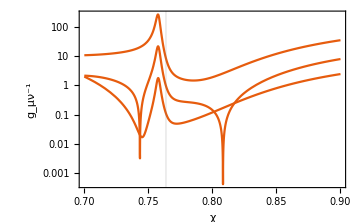

```mathematica
κsec=-0.4;
Show[Plot[Abs[Inverse[gNumeric[5,κsec,c]]⟦#[[1]],#[[2]]⟧],{c,0.7,0.9},GridLines->{{qptA[κsec]},None},PlotRange->All,FrameLabel->{"χ","g_μν^-1"},ImageSize->Medium,ScalingFunctions->"Log"]&/@{{1,1},{1,2},{2,2}}]
```

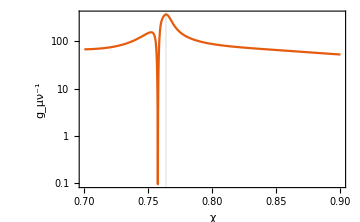
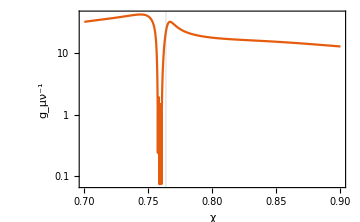
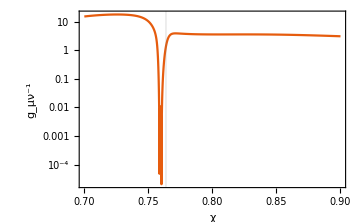

```mathematica
κsec=-0.4;
Plot[Abs[Inverse[gNumericOrder[5,κsec,c,2,5]]⟦#[[1]],#[[2]]⟧-Inverse[gNumeric[5,κsec,c]]⟦#[[1]],#[[2]]⟧],{c,0.7,0.9},GridLines->{{qptA[κsec]},None},FrameLabel->{"χ","g_μν^-1"},ImageSize->Medium,ScalingFunctions->"Log",PlotRange->All]&/@{{1,1},{1,2},{2,2}}
```

## Metric tensor determinant

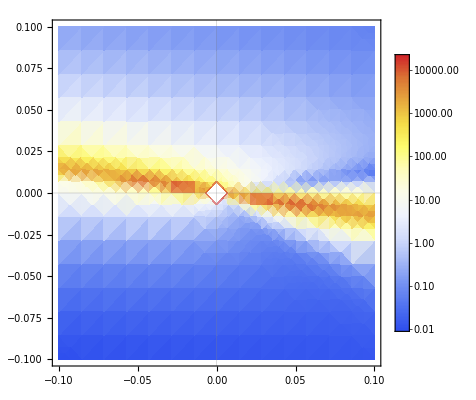

```mathematica
DensityPlot[Abs@Det[gNumeric[5,-1/4+z1,(√5)/3+z2]],{z1,-0.1,0.1},{z2,-0.1,0.1},ScalingFunctions->"Log",PlotLegends->Automatic,ColorFunction->"TemperatureMap"]
```

## Metric tensor on χ=0

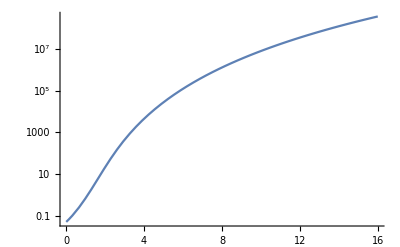

```mathematica
Plot[gC[l,0][[2,2]],{l,-0,16},ScalingFunctions->"Log"](*N=5*)
```

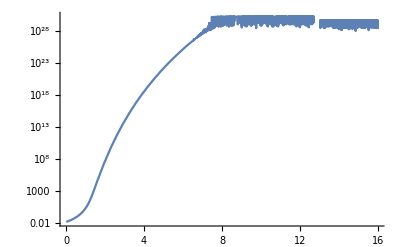

```mathematica
Plot[gC[l,0][[2,2]],{l,-0,16},ScalingFunctions->"Log"](*N=20*)
```

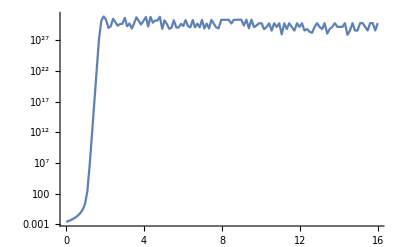

```mathematica
Plot[gC[l,0][[2,2]],{l,-0,16},ScalingFunctions->"Log",PlotRange->All,PlotPoints->3](*N=100*)
```

## Metric tensor of k-th state manifold

```mathematica
optDen={Evaluate@densityPlotOptions,PlotPoints->20,ImageSize->Medium};
components[k_]:={
DensityPlot[ArcTan[gkC[y,x,k]⟦1,1⟧],{y,-0.2,0.4},{x,0,1},Evaluate@optDen],
DensityPlot[ArcTan[gkC[y,x,k]⟦2,2⟧],{y,-0.2,0.4},{x,0,1},Evaluate@optDen],
DensityPlot[ArcTan[gkC[y,x,k]⟦1,2⟧],{y,-0.2,0.4},{x,0,1},Evaluate@optDen]}
```

#### Metric tensor determinant

```mathematica
MetricDeterminant[k_,pp_]:=DensityPlot[ArcTan@Det[gkC[λ,χ,k]],{λ,-2.1,5},{χ,-1.55,1.55},Evaluate@densityPlotOptionsWithoutLegend,PlotPoints->pp,PlotRange->Full,ImageSize->190]
```

```mathematica
MetricDeterminant[k_,pp_]:=DensityPlot[ArcTan@Det[gkC[λ,χ,k]],{λ,0.3,1.2},{χ,0.05,0.75},Evaluate@densityPlotOptionsWithoutLegend,PlotPoints->pp,PlotRange->Full,ImageSize->190]
```

```mathematica
metDeterminants=MetricDeterminant[#,50]&/@Range[6];
```

```mathematica
metDeterminantsGrid=plotGrid[
{{metDeterminants[[1]],metDeterminants[[2]]},
{metDeterminants[[3]],metDeterminants[[4]]},
{metDeterminants[[5]],metDeterminants[[6]]}},520,690,ImagePadding->45]
```

```mathematica
Export[NotebookDirectory[]<>"../ourArticles/geometry_of_LMG/images/N=5_metricDeterminants.pdf",metDeterminantsGrid,"AllowRasterization"->True,ImageResolution->800];
```

## Christoffel symbols

### Christoffel symbols

```mathematica
diff=441;
atang1tab1=Flatten[ParallelTable[{λ,χ,ArcTan@G1[λ,χ]⟦#⟧},{λ,-2.,2.,4/diff},{χ,-1.45,1.45,3/diff},Method->"FinestGrained"],1]&/@{1,2,3};
atang2tab1=Flatten[ParallelTable[{λ,χ,ArcTan@G2[λ,χ]⟦#⟧},{λ,-2.,2.,4/diff},{χ,-1.45,1.45,3/diff},Method->"FinestGrained"],1]&/@{1,2,3};
```

```mathematica
gammaopt={FrameTicks->{{Range[-5,5,1],None},{Range[-4,6,1],None}},PlotRangePadding->0,PerformanceGoal->"Quality",PlotTheme->"Default",Evaluate@font,AspectRatio->2/3,PlotRange->Full,FrameLabel->MaTeX/@{"",""},ColorFunction->"TemperatureMap"};
barA=BarLegend[{"Temperature",{-π/2,π/2}},LegendLayout->"Row",Evaluate@font,LegendMarkerSize->220,Ticks->{{-0.7854,"-π/4"},{-1.57,"-π/2"},{0,0},{0.7854,"π/4"},{1.57,"π/2"}}];
```

```mathematica
{{gammasDen111,gammasDen121,gammasDen122},{gammasDen211,gammasDen221,gammasDen222}}=Table[
ListDensityPlot[{atang1tab1⟦#⟧,atang2tab1⟦#⟧}[[i]],Axes->False,PlotTheme->"Detailed",PlotLegends->False,
Evaluate@gammaopt,InterpolationOrder->2,PlotRangeClipping->False,
If[(i==1&&#==1)||(i==1&&#==3)||(i==2&&#==2),
Epilog->{Text[MaTeX["\\kappa"],{0,-2.1}],Text[Rotate[MaTeX["\\chi"],π/2],{-2.9,0}]},
Epilog->{Text[MaTeX["\\kappa"],{0,-2.1}]}]
]
&/@{1,2,3},{i,1,2}];
gammas=Quiet@ResourceFunction["PlotGrid"][{{gammasDen111,gammasDen121},{gammasDen122,gammasDen211},{gammasDen221,gammasDen222}},ImageSize->379,PlotLabels->Placed[MaTeX/@{"\\Gamma_{111}","\\Gamma_{121}","\\Gamma_{122}","\\Gamma_{211}","\\Gamma_{221}","\\Gamma_{222}"},{0.16,0.5}]];
```

```mathematica
plgammas=ImageCrop@Show[{
GraphicsColumn[{gammas,Row@{Spacer[25],barA}},Spacings->-20],
Graphics[Inset[MaTeX["\\text{atan}(\\Gamma_{\\alpha\\beta\\gamma})"],{77,-367}]]
},ImageSize->363]
```

-Graphics-

```mathematica
Export["/Users/strelda/synced Documents/phd/our/Quantum geometry of critical bosonic systems/img/N=10_gammas.pdf",plgammas,"AllowRasterization"->True,ImageResolution->3000];
```

## Ricci scalar

#### Analysis in parametric space

```mathematica
barRic=BarLegend[{"Temperature",{-π/2,π/2}},LegendLayout->"Column",Evaluate@font,LegendMarkerSize->128,Ticks->{{-0.7854,"-π/4"},{-1.57,"-π/2"},{0,0},{0.7854,"π/4"},{1.57,"π/2"}},LegendLabel->MaTeX["\\text{atan}(R)"],LegendMargins->0];
```

```mathematica
riccitab=Quiet@Flatten[ParallelTable[{λ,χ,ArcTan@Ric[10,λ,χ]},{λ,-4.1,4.1,8./151},{χ,0.,1.8,1.8/151}],1];
```

```mathematica
plRic=Show[{ListDensityPlot[riccitab,
Evaluate@font,PlotLegends->False,PlotRange->All,PlotRangePadding->0,AspectRatio->1/2,PerformanceGoal->"Quality",
InterpolationOrder->2,Frame->True,(*PlotTheme->"Default",*)FrameLabel->MaTeX/@{"",""},ImageSize->344,FrameTicks->{{Range[0,2,0.5],None},{Range[-4,4,2],None}},
ColorFunction->"Temperature",PlotRangeClipping->False,ImagePadding->{{40,50},{30,1}},
Epilog->{Text[MaTeX["\\kappa"],{0,-0.3}],Text[Rotate[MaTeX["\\chi"],π/2],{-5.,0.9}],
								Inset[barRic,{4.8,0.78}]
								}
],
Plot[{0,0.6,1.3},{x,-4,4},PlotStyle->{{Black,Dashed,Thickness[0.01]}}],
ListPlot[{{{1.5,0.5}},{{-1.5,1.5}},{{1,1}}}[[#]],PlotStyle->{Red,Darker@Green,Darker@Blue}[[#]],PlotMarkers->{{"★","•","◆"}[[#]],16}]&/@Range[3]
}]
```

-Graphics-

```mathematica
Export["/Users/strelda/synced Documents/phd/our/Quantum geometry of critical bosonic systems/img/ricci_N=10.pdf",plRic,"AllowRasterization"->True,ImageResolution->800];
```

### Convergence with N

#### phase 2

```mathematica
ph2={{1.5`30,0.5`30},{-1.5`30,1.5`30},{1.`30,1.`30}};
ph2Data=ParallelTable[{n,Ric[n,pt[[1]],pt[[2]]]},{pt,ph2},{n,5,60,1}];
```

$Aborted

```mathematica
ph2DataA=Transpose@Map[(MovingAverage[#,1]&),Transpose[#]]&/@ph2Data;
```

```mathematica
ricciNPlot=ListPlot[ph2DataA,PlotStyle->{Red,Darker@Green,Darker@Blue},PlotMarkers->{"★","•","◆"},PlotRange->{{4,61},{-6.2,-2.2}},
PlotLegends->Placed[PointLegend[{"(1.5,0.5)","(-1.5,1.5)","(1,1)"},LegendLayout->{"Row",1}],{0.6,0.85}],Frame->True,
Evaluate@font,PlotTheme->"Default",FrameLabel->MaTeX/@{"",""},FrameTicks->{{Range[-10,0,1],None},{Range[0,60,20],None}},
PlotRangeClipping->False,PlotRangePadding->0,AspectRatio->1/3,ImageSize->335,
Epilog->{Text[MaTeX["N"],{32.5,-7.}],Text[Rotate[MaTeX["R"],π/2],{-1.,-4.2}]}]
```

-Graphics-

```mathematica
Export["/Users/strelda/synced Documents/phd/our/Quantum geometry of critical bosonic systems/img/ricci_N_convergence.pdf",ricciNPlot,"AllowRasterization"->True,ImageResolution->800];
```

#### horizontal sections

```mathematica
diff=251;
```

```mathematica
SectionCols={{Red,DotDashed},{Blue,Dashed},Darker@Green};
OptSection={
Axes->False,Evaluate@font,Frame->True,PlotTheme->"Default",AspectRatio->1.7/7,
FrameLabel->MaTeX/@{"",""},PlotRange->{{-4.1,4.1},Automatic},PlotRangeClipping->False,PlotRangePadding->0,
PlotStyle->SectionCols,ImageSize->340,
GridLines->{None, {-4}},FrameTicks->{{Range[-90,100,30],None},{Range[-4,4,2],None}}
};
```

```mathematica
negsec10=ParallelTable[{λ,Ric[5,λ,0.`20]},{λ,-4.`20,1.`20,13/diff}];
negsec50=ParallelTable[{λ,Ric[10,λ,0.`20]},{λ,-4.`20,1.`20,13/diff}];
negsec100=ParallelTable[{λ,Ric[50,λ,0.`20]},{λ,-4.`20,1.`20,13/diff}];
```

```mathematica
ph1Plot=ListLinePlot[{negsec10,negsec50,negsec100},PlotRange->{{-4.01,4.01},{-68,5}},Evaluate@OptSection,PlotLegends->Placed[LineLegend[SectionCols,{"N=5","N=10","N=50"},LegendMarkerSize->15],{0.9,0.46}],
Epilog->{Text[MaTeX["\\chi=0"],{-3.4,-55}],Text[Rotate[MaTeX["R"],π/2],{-4.8,-30}]}]
```

```mathematica
negsecc5=ParallelTable[{λ,Ric[5,λ,0.3`20]},{λ,-4.`20,4.`20,10/diff}];
negsecc10=ParallelTable[{λ,Ric[10,λ,0.3`20]},{λ,-4.`20,4.`20,10/diff}];
```

```mathematica
negsecc50=ParallelTable[{λ,Ric[50,λ,0.3`20]},{λ,-4.`20,4.`20,10/diff}];
```

```mathematica
negsecc50A=Transpose@Map[(MovingAverage[#,3]&),Transpose[negsecc50]];
```

```mathematica
ph2Plot=ListLinePlot[{negsecc5,negsecc10,negsecc50A},PlotRange->{{-4.01,4.01},{-80,50}},Evaluate@OptSection,InterpolationOrder->1,Epilog->{Text[MaTeX["\\chi=0.6"],{-3.4,-61}],Text[Rotate[MaTeX["R"],π/2],{-4.8,-10}]}]
```

```mathematica
negseccc5=ParallelTable[{λ,Ric[5,λ,1.3`20]},{λ,-4.`20,4.`20,13/diff}];
negseccc10=ParallelTable[{λ,Ric[10,λ,1.3`20]},{λ,-4.`20,4.`20,13/diff}];
```

```mathematica
negseccc50=ParallelTable[{λ,Ric[50,λ,1.3`20]},{λ,-4.2`20,4.2`20,13/diff}];
```

```mathematica
negseccc50A=Transpose@Map[(MovingAverage[#,10]&),Transpose[negseccc50]];
```

```mathematica
ph3Plot=ListLinePlot[{negseccc5,negseccc10,negseccc50A},PlotRange->{{-4.01,4.01},{-4.1,-0.5}},FrameTicks->{{Range[-6,0,1],None},{Range[-4,4,2],None}},Evaluate@OptSection,Epilog->{Text[MaTeX["\\chi=1.3"],{-3.4,-3.1}],Text[MaTeX["\\kappa"],{0,-5.2}],Text[Rotate[MaTeX["R"],π/2],{-4.8,-2.5}]},InterpolationOrder->2]
```

```mathematica
ricciSectionsPlot=ImageCrop@ResourceFunction["PlotGrid"][{{ph1Plot},{ph2Plot},{ph3Plot}},ImageSize->348]
```

-Graphics-

```mathematica
Export["/Users/strelda/synced Documents/phd/our/Quantum geometry of critical bosonic systems/img/ricci_convergence.pdf",ricciSectionsPlot,"AllowRasterization"->True,ImageResolution->800];
```

#### showing that R = R (κ) in Phase I

```mathematica
negse5=ParallelTable[{λ,Ric[100,λ,0.`20]},{λ,-6.`20,1.`20,10/15}];
negse10=ParallelTable[{λ,Ric[100,λ,0.3`20]},{λ,-6.`20,1.`20,10/15}];
```

```mathematica
negse50=ParallelTable[{λ,Ric[100,λ,0.6`20]},{λ,-6.`20,1.`20,10/15}];
```

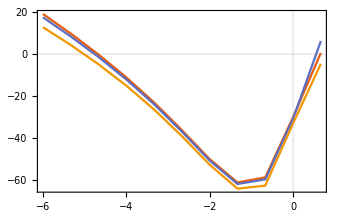

```mathematica
ph2Plot=ListLinePlot[{negse5,negse10,negse50}]
```

# Geodesics

```mathematica
ricTab[λmin_,λmax_,χmin_,χmax_,diff_]:=Flatten[ParallelTable[{λ,χ,ArcTan@Ric[λ,χ]},{λ,λmin,λmax,(λmax-λmin)/diff},{χ,χmin,χmax,(χmax-χmin)/diff}],1];
```

```mathematica
detTab[λmin_,λmax_,χmin_,χmax_,diff_]:=Flatten[ParallelTable[{λ,χ,Det@gC[λ,χ]},{λ,λmin,λmax,(λmax-λmin)/diff},{χ,χmin,χmax,(χmax-χmin)/diff}],1];
```

```mathematica
bgPlotOptions={AspectRatio->1/2,PlotRangePadding->0,Evaluate@font,ImageSize->320,PlotRangePadding->0,FrameLabel->MaTeX/@{"",""},ColorFunction->ColorData[{"GrayTones",{1,0}}]};
barRic=BarLegend[{ColorData[{"TemperatureMap",{-π/2,π/2}}],{-π/2,π/2}},LegendLayout->"Row",Evaluate@font,LegendMarkerSize->230,Ticks->{{-π/2+0.001,"π/2"},{0,"0"},{π/2-0.001,"π/2"}}];
```

```mathematica
tmax=10;
eq={
λ''[t]+G1[λ[t],χ[t]].{ λ'[t]^2,2 λ'[t]χ'[t], χ'[t]^2}==0,
χ''[t]+G2[λ[t],χ[t]].{ λ'[t]^2,2 λ'[t]χ'[t], χ'[t]^2}==0
};
```

```mathematica
singStop=5 10^-3;
stopEvent={WhenEvent[λ[t]>4||χ[t]>1.02||λ[t]<-5.1||χ[t]<=0,"StopIntegration"]};
```

```mathematica
diabolicsEvent=Map[(WhenEvent[#,"StopIntegration"]&),Norm[{λ[t],χ[t]}-diabolicPoints[nn][[#]]]<singStop&/@Range[Length[diabolicPoints[nn]]]];
```

```mathematica
cauchy[l1_,x1_,l2_,x2_]:={λ[0]==l1,χ[0]==x1,λ'[0]==l2,χ'[0]==x2};
```

```mathematica
sol[λ0_,χ0_,λd0_,χd0_,tmax_:10,prec_:10,workingprecision_:30]:=Quiet@NDSolve[Join[eq,cauchy[λ0,χ0,λd0,χd0],stopEvent,diabolicsEvent],{λ,χ},{t,0,tmax},Method->{"TimeIntegration"->{"ExplicitRungeKutta","DifferenceOrder"->8}},PrecisionGoal->prec,AccuracyGoal->prec,WorkingPrecision->workingprecision]
sol::usage="sol[λ0_,χ0_,λd0_,χd0_,tmax_:10,prec_:10,workingprecision_:30] 
Calculates the geodesic for: 
{λ0,χ0}=initial values, 
{λd0,χd0}=initial velocities, 
tmax=max. time of evolution, 
prec=WorkingGoal,AccuracyGoal of NDSolve,
workingprecision=WorkingPrecision of NDSolve.";
```

```mathematica
geodBall[λi_,χi_,tmax_,N_, prec_,workingprecision_]:=ParallelTable[sol[λi,χi,Cos[θ],Sin[θ],tmax,prec,workingprecision],{θ,0,2π,2π/N}];
geodBall::usage="Evolve N geodesics from {λi,χi} for short time tmax. prec=PrecisionGoal=AccuracyGoal, workingprecision=WorkingPrecision of NDSolve.
λi_,χi_,tmax_,N_,prec_,workingprecision_";
```

```mathematica
bar2=BarLegend[{Blend[{RGBColor[0,1,1],RGBColor[1,0,0]},#]&,{0,1}},LegendMarkerSize->{135,10},Ticks->{{0,"0"},{1,"1"}},
LegendLayout->"Row",Evaluate@font];
```

### Many geods

```mathematica
detTabm=detTab[-4.02,4.02,0,1.02,300];
```

```mathematica
bar1=BarLegend[{ColorData[{"GrayTones",{1,0}}],{0,1}},LegendMarkerSize->{135,10},Ticks->{{0.06,"10^-8"},{0.5,"10^-3"},{0.94,"10^2"}},
LegendLayout->"Row",Evaluate@font];
```

```mathematica
bgDet=ListDensityPlot[detTabm,PlotLegends->False,
ScalingFunctions->"Log",PlotRange->All,
ImageSize->340,AspectRatio->1,Axes->False,PlotTheme->"Detailed",
FrameLabel->{"",""},PlotRangeClipping->False,
Evaluate@bgPlotOptions,FrameTicks->{{Range[0,1,0.2],None},{Range[-4,4,2],None}},
Epilog->{
Text[Rotate[MaTeX["\\chi"],π/2],{-4.8,0.5}],Text[MaTeX["\\kappa"],{0,-0.08}],Text[MaTeX["u"],{-3.9,-0.133}],Text[MaTeX["\\det (g)"],{0.5,-0.135}],
Inset[bar1,{2.3,-0.16}],Inset[bar2,{-2.35,-0.16}]
},ImagePadding->{{36,3},{66,0}},ImageMargins->0
];
```

```mathematica
solMulti=Flatten[ParallelTable[sol[-4,χ0,1,0,HeavisideTheta[0.88-χ0]50+20,10,100],{χ0,0.01,1.,0.02}],1];
```

```mathematica
solMulti1=Select[solMulti,(Length[#]==2)&];
```

```mathematica
solMultiZ1=Flatten[ParallelTable[sol[-4.`50,χ0,1.`50,0.`50,70,8,100],{χ0,0.7918`50,0.793`50,0.0002}],1];
```

```mathematica
solMultiZ2=Flatten[ParallelTable[sol[-4.`50,χ0,1.`50,0.`50,70,8,100],{χ0,0.532,0.568,0.002}],1];
```

```mathematica
geods5=Show[{
Show[{bgDet,PlotSolsSpeed[solMulti],PlotSolsSpeed[solMultiZ1],PlotSolsSpeed[solMultiZ2]}]
},PlotRangeClipping->False,ImageSize->335]
```

-Graphics-

```mathematica
Export["/Users/strelda/Library/Mobile Documents/com~apple~CloudDocs/Files/synced Documents/phd/our/Quantum geometry of critical bosonic systems/img/N=5_geods.pdf",geods5,"AllowRasterization"->False,ImageResolution->1800];
```

### Intro visualization

#### random zoom into geodesic ball

```mathematica
solMulti=Flatten[ParallelTable[sol[1,0.05,Cos[p],Sin[p],3,10,20],{p,{(19 π)/150,(41 π)/300,(11 π)/75+0.003}}],1];
```

```mathematica
geodball=Flatten[geodBall[3.541,0.1685,0.05,10,10,10],1];
```

```mathematica
(*ricTabm=ricTab[0.98,4,0.03,0.33,20];
bgRic=ListContourPlot[ricTabm,PlotLegends->Automatic,PlotRange->All,Contours->50];*)
```

```mathematica
detTabm=detTab[0.98,4,0.03,0.33,150];
```

```mathematica
bgDet=ListDensityPlot[detTabm,PlotLegends->Automatic,PlotRange->All,Evaluate@bgPlotOptions,FrameTicks->{{Range[0,1,0.1],None},{Range[1,4,1],None}}];
```

```mathematica
Show[{bgDet,PlotSols[geodball,col="Blue"],PlotSolsSpeed[solMulti]},PlotRange->{{0.98,4},{0.03,0.33}}]
```

-Graphics-

#### big ball

```mathematica
bar1=BarLegend[{ColorData[{"GrayTones",{1,0}}],{0,1}},LegendMarkerSize->122,Ticks->{{0,"10^-6"},{0.5,"10^-1"},{1,"10^4"}},
LegendLayout->"Column",Evaluate@font,LegendLabel->MaTeX["\\det(g)"]];
```

```mathematica
solMulti2=Flatten[ParallelTable[sol[1,0,0.3Cos[p],0.3Sin[p],100,5,20],{p,{0.47`50,0.7`50,1.1`50,2.`50,3.05`50}}],1];
```

```mathematica
detTabm2=detTab[-1.01,4.01,-0.01,0.91,300];
```

```mathematica
bgDet2=ListDensityPlot[detTabm2,PlotLegends->Placed[bar1,{{1,.55},{0.45,0.5}}],ScalingFunctions->"Log",PlotRange->All,ImageSize->370,
FrameTicks->{{Range[0,1,0.3],None},{Range[-10,10,1],None}},Evaluate@bgPlotOptions,Axes->False,PlotRangePadding->0,PlotRangeClipping->False,Epilog->{Text[Rotate[MaTeX["\\chi"],π/2],{-1.61,0.45}],Text[MaTeX["\\kappa"],{1.5,-0.18}],Text[MaTeX["u"],{1.65,0.85}],Inset[bar2,{2.7,0.8}]}
];
```

```mathematica
ilfig=Show[{bgDet2,PlotSolsSpeed[solMulti2]}]
```

-Graphics-

```mathematica
Export["/Users/strelda/Library/Mobile Documents/com~apple~CloudDocs/Files/synced Documents/phd/our/compose/geods_illustration.pdf",ilfig,"AllowRasterization"->False,ImageResolution->1800];
```

## Geodesic balls

```mathematica
geodbg = DensityPlot[Det[gC[λ,χ]],{λ,-4,2},{χ,-3,3},Evaluate@font, PlotRange->Full,PlotLegends->None,ColorFunction->ColorData[{"GrayTones",{1,0}}],FrameLabel->{-Graphics-,-Graphics-},PlotPoints->20,ScalingFunctions->"Log10",PlotRange->Full,ImageSize->310];
```

```mathematica
balls=ParallelTable[geodBall[λi,χi,0.1,10,10,10],{λi,-1,2,0.5},{χi,0,3,0.5}];
```

```mathematica
Show@PlotSolsSpeed[Flatten[balls,3]]
```

-Graphics-

## Boundary value problem

```mathematica
dirichlet[i1_,i2_,f1_,f2_]:={λ[0]==i1,χ[0]==i2,λ[tmax]==f1,χ[tmax]==f2};
```

```mathematica
(*WorkingPrecision->20,Method->"StiffnessSwitching"*)
```

```mathematica
Timing@NDSolve[Join[eq,dirichlet[0,0,0,0.2]],{λ,χ},{t,0,tmax},PrecisionGoal->2,AccuracyGoal->2,WorkingPrecision->100,Method->"ExplicitRungeKutta"]
```

```mathematica
(*solP=ParametricNDSolve[Join[eq,dirichlet[0,0,0.3,f2]],{λ,χ},{t,0,tmax},{f2},PrecisionGoal->2,AccuracyGoal->2]
ParametricPlot[Evaluate@Table[{λ[f2][t],χ[f2][t]}/.solP,{f2,0,2,1}],{t,0,10},PlotRange->All]*)
```

```mathematica
Plot[Evaluate[x[t]/.sols],{t,0,10},PlotStyle->{Black,Blue,Green}]
```

```mathematica
solM=Quiet@ParallelTable[NDSolve[Join[eq,dirichlet[0,0,1,i]],{λ,χ},{t,0,tmax},PrecisionGoal->2,AccuracyGoal->2],{i,0,0.8,0.2}]
```

$Aborted

```mathematica
geodBoundary=ParametricPlot[{λ[t],χ[t]}/.solM2,{t,0,tmax},PlotRange->All,Frame->True,PlotStyle->Green];
Show[{geodbg,geodBoundary}]
```

## Principal directions

## Minimal valley - eigensystem of the metric tensor

```mathematica
(*Separatrix and diabolic point coordinates plot*)
separatrix=ContourPlot[χ^2==(λ-1)/(λ-2),{λ,-10,2},{χ,-1.2,1.2},ContourStyle->Red];
diabolicPointsPlot=ListPlot[{diabolicPoints[nn],{#[[1]],-#[[2]]}&/@diabolicPoints[nn]},PlotStyle->{{Red,PointSize[0.02]}}];
```

Part::partd: Part specification nn⟦1⟧ is longer than depth of object.

Part::partd: Part specification nn⟦2⟧ is longer than depth of object.

Eigenvectors of the symmetric matrix are orthogonal on the Manifold, meaning v_1(λ,χ).g_μν(λ,χ).v_2(λ,χ)=0

```mathematica
Show[{EigenVectorPlot[H,"min","VectorPoints"->10,"Zoom"->0.5,"ZoomCenter"->{1.5,1.0}],separatrix,diabolicPointsPlot}]
```

-Graphics-

```mathematica
Show[{EigenVectorPlot[H,"min","VectorPoints"->20],separatrix,diabolicPointsPlot}]
```

-Graphics-

```mathematica
EigenStreamPlot[]
```

-Graphics-

```mathematica
EigenStreamPlot["Zoom"->0.03,"ZoomCenter"->{-1.5,0.82}]
```

-Graphics-

```mathematica
EigenStreamPlot["Zoom"->0.1,"ZoomCenter"->{-0.3,0.7}]
```

-Graphics-

# Holstein-Primakoff double well impotential structure

```mathematica
HPexact[λ_,χ_,x_,p_]:=-1/2+(1-λ)/2 x^2+(λ-χ^2)/4 x^4-(χ x^3)/2 √(2-x^2-p^2)-χ^2/4 p^4+p^2/4(2+(λ-2 χ^2)x^2-2χ x √(2-x^2-p^2));
HP=Compile[{{λ,_Real},{χ,_Real},{x,_Real},{p,_Real}},Module[{x2,p2,χ2},
(*-1/2+(1-λ)/2 x^2+(λ-χ^2)/4 x^4-(χ x^3)/2 √(2-x^2-p^2)-χ^2/4 p^4+p^2/4(2+(λ-2 χ^2)x^2-2χ x √(2-x^2-p^2))*)
x2=x^2;
p2=p^2;
χ2=χ^2;
-1/2+(1-λ)/2 x2+(λ-χ2)/4 x2^2-(χ x^3)/2 √(2-x2-p2)-χ2/4 p2^2+p2/4(2+(λ-2χ2)x2-2χ x √(2-x2-p2))
],Evaluate@compileOptions];
```

```mathematica
D[HPexact[λ,χ,x,p],χ]
```

-1/2 x^3 √(2-p^2-x^2)-(p^4 χ)/2-(x^4 χ)/2+1/4 p^2 (-2 x √(2-p^2-x^2)-4 x^2 χ)

```mathematica
λsec5=Table[{χ,Det[gC[2,χ]]},{χ,0,3,0.02}];
```

```mathematica
λsec15=Table[{χ,Det[gC[2,χ]]},{χ,0,3,0.02}];
```

```mathematica
λsec30=ParallelTable[{χ,Det[gC[2,χ]]},{χ,0.1,3,0.02}];
```

```mathematica
λsec200=ParallelTable[{χ,Det[gC[2,χ]]},{χ,0.1,3,0.02}]
```

```mathematica
ListLinePlot[{λsec5,λsec15,λsec30,λsec200},FrameLabel->MaTeX/@{"\\chi","\\det g(\\lambda=2,\\chi)"},Evaluate@plotOptions,PlotRange->{0,0.005},PlotLegends->{"N=5","N=15","N=30","N=200"},FrameTicks->{{Range[0,0.01,0.001],None},{Range[0,10,0.5],None}}]
```

-Graphics-

### Section dependence on the coordinate

```mathematica
Secp[λ_,χ_]:=Module[{x},
(*Plot the impotential section p=0*)
Plot[HP[λ,χ,x,0],{x,-√2,√2},Evaluate@font,Frame->True,FrameLabel->MaTeX/@{"x","H(x,0)"},Axes->False,PlotStyle->Red,PlotRange->{-2,2},ImageSize->Medium]
]
SecH[λ_,χ_]:=Module[{x,p},
(*Plot the impotential for fixed λ,χ.*)
Plot3D[Re@HP[λ,χ,x,p],{x,-√2,√2},{p,-√2,√2},AxesLabel->MaTeX/@{"x","p","H(\\lambda,\\chi)"},PlotLegends->False,MeshFunctions->{#2&},Mesh->5,ColorFunction->"TemperatureMap",RegionFunction->Function[{x,p},x^2+p^2<2]]
]
FindMinH[λ_,χ_]:=Module[{prec,dif,H,all,vals,selectionRule,x,p},
(*for prec=10^-15 it calculates the minimum of (x,p) curve of classical H, or for prec=10^-4 it finds more possible minimas*)
prec=10^-15;
dif=0.01;
H[x_,p_]:=HPexact[λ,χ,x,p];
all=Flatten[Table[{x,p,If[x^2+p^2<2,H[x,p],10^11]},{x,-√2,√2,dif},{p,-√2,√2,dif}],1];
(*select values and find the minimas, selectionRule will be zero at the minimas*)
vals=Transpose[all][[3]];
selectionRule=Chop[vals-Min[vals],prec];
(*pick only values and coordinates corresponding to minimas*)
Pick[all,selectionRule,0]
]
Hess[λ_,χ_,x_,p_]:=Module[{hessElement,x1,p1},
(*calculate the Hessian at specific point*)
hessElement[l1_,l2_]:=D[HPexact[λ,χ,x1,p1],l1,l2];
Det[{{hessElement[x1,x1],hessElement[x1,p1]},{hessElement[p1,x1],hessElement[p1,p1]}}/.{x1->x,p1->p}]
]
HessInMinimum[λ_,χ_]:=Module[{xmin,pmin},
(*calculate the Hessian of the minimum in (x,p) plot. Minimum is found using FindMinH[λ,χ]*)
{xmin,pmin}=FindMinH[λ,χ][[1,1;;2]];
Hess[λ,χ,xmin,pmin]
]
FindMinHCoord[λ_,χ_]:=Module[{pts,val},
(*extract the coordinate of the minimas, suitable for plotting and finding discontinuities*)
pts=FindMinH[λ,χ];
(*check if there is only one minimum*)
If[Length[pts]==1,
val=√(pts[[1,1]]^2+pts[[1,2]]^2),
val=Mean[√((#[[1]])^2+(#[[2]])^2)/@pts]];
{Length[pts],val}
]
```

#### Manipulate

```mathematica
minDirectionPlot=DensityPlot[Det[gC[λ,χ]],{λ,-5,5},{χ,-2,2},PlotLegends->False,ColorFunction->"TemperatureMap",Evaluate@densityPlotOptions,PlotPoints->50,ScalingFunctions->"Log",ImageSize->Small];
```

```mathematica
Manipulate[GraphicsRow[{
Show[minDirectionPlot,ListPlot[{{λ,χ}},PlotStyle->Red,PlotMarkers->{Automatic,Medium}]],
(*Secp[λ,χ],*)
SecH[λ,χ]
},ImageSize->500],{λ,-5,5},{χ,-2,2}]
```

### Plot the minima coordinates and number of minima, viz Julia

# Geodesics vs. lines

## Import and check paths

### maxtheta = 1

```mathematica
geodbg=PrintDeterminant[nn,-1,10,0,1,5,1,1];
```

```mathematica
path=Import["/media/Data/MFF/Diplomová práce/code/savedData/solMulti_N=5_maxtheta=1.m"];
```

```mathematica
λmaxS=1;
```

```mathematica
paths=Map[Flatten,{λ,χ}/.path];
numPaths=Dimensions[paths]⟦1⟧;numPaths
endTimes=paths⟦#,1,1,1,2⟧&/@Range[Dimensions[paths]⟦1⟧]
```

51

{1.24447,4.80265,10.,4.24072,4.27588,4.46353,3.98251,10.,3.63296,1.06135,3.41819,3.18889,1.02902,1.00889,2.77999,2.68695,2.60093,2.4407,0.911255,0.892428,2.1306,2.03615,0.841666,1.87785,10.,10.,10.,1.52124,10.,1.36782,10.,10.,10.,1.15337,1.06729,1.03117,10.,0.934925,0.895426,0.857071,0.830349,0.794177,0.78259,0.756595,10.,0.726163,0.745843,10.,0.536244,0.751511,0.483283}

```mathematica
Show[{geodbg,PlotSols[path]}]
```

```mathematica
tmaxS[i_]:=τ/.Quiet@FindRoot[λmaxS-λ[τ]/.path[[i]][[1]],{τ,3}][[1]]
```

```mathematica
{λin,χin}={0,0};
num=500;
lineForSolve[tt_,j_]:=Module[{λfinal,χfinal},
{λfinal,χfinal}=Flatten[{λ[tt],χ[tt]}/.path⟦j⟧];
{{λ[t]->λin+((λfinal-λin)t)/tt,χ[t]->χin+((χfinal-χin)t)/tt,λ'[t]->(λfinal-λin)/tt,χ'[t]->(χfinal-χin)/tt}}];
line[j_]:=Module[{tt,λfinal,χfinal},
tt=tmaxS[j];
{λfinal,χfinal}=Flatten[{λ[tt],χ[tt]}/.path⟦j⟧];
{{λ->Interpolation[{{0,λin},{tmaxS[j],λfinal}},InterpolationOrder->1],χ->Interpolation[{{0,χin},{tmaxS[j],χfinal}},InterpolationOrder->1]}}
]
```

```mathematica
Show[{geodbg,PlotSols[path],PlotSols[Table[line[j],{j,1,numPaths}],"Cyan"]},ImageSize->Large]
```

-Graphics-

## Distance from 0,1

```mathematica
tmaxM=10;
```

```mathematica
L=√({λ'[t],χ'[t]}.gC[λ[t],χ[t]].{λ'[t],χ'[t]});
numD=10;
Dstep=tmaxM/numD;
```

```mathematica
DtMax=7;
```

```mathematica
Dline=Flatten@Map[NIntegrate[L/.line[#],{t,0,DtMax}]&,Range[numPaths]];
```

```mathematica
Dpath=Flatten@NIntegrate[L/.path,{t,0,DtMax}];
```

```mathematica
ListPlot[{Dline,Dpath},PlotLegends->{"Dline","Dpath"}]
```

-Graphics-

```mathematica
DlineM=Table[Flatten@Map[NIntegrate[L/.line[#],{t,0,t1}]&,Range[numPaths]],{t1,Dstep,tmaxM-Dstep,Dstep}];
```

```mathematica
ListLinePlot[DlineM]
```

-Graphics-

```mathematica
DpathM=Accumulate@Table[Flatten@NIntegrate[L/.path,{t,t1,t1+Dstep}],{t1,Dstep,tmaxM-Dstep,Dstep}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {7.97557667141115}. NIntegrate obtained 0.216705 and 0.0334233 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {7.86327}. NIntegrate obtained 0.169694 and 0.00379893 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {7.87303}. NIntegrate obtained 0.178875 and 0.00237912 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
ListLinePlot[DpathM]
```

-Graphics-

```mathematica
ListPlot[{DlineM⟦#⟧,DpathM⟦#⟧},PlotLegends->{"Dline","Dpath"}]&/@Range[numD-1]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Fidelity using quenches

```mathematica
Fidelity[λ1_,χ1_,λ2_,χ2_]:=Abs[GroundState[λ1,χ1].GroundState[λ2,χ2]];
Susceptibility[λ_,χ_]:={-ND[Log[Fidelity[λ,χ,λ+l,χ]],{l,2},0],-ND[Log[Fidelity[λ,χ,λ,χ+c]],{c,2},0]}
```

```mathematica
InfidelityDif[t_,dt_,path_]:=Module[{λ,χ},
λ[T_]:=path[[1,1,2]][T];
χ[T_]:=path[[1,2,2]][T];
{t,1-Fidelity[λ[t],χ[t],λ[t+dt],χ[t+dt]]}
]
```

```mathematica
energyDif[λ_?NumericQ,χ_?NumericQ]:=Module[{en},
en=EigensystemSorted[λ,χ][[1]];
en[[2]]-en[[1]]
]
```

```mathematica
zeroCondplot=ContourPlot[ND[energyDif[λ,c],c,χ]==0,{λ,-1,3},{χ,-1,1},PlotPoints->20,ContourStyle->Darker@Green,PerformanceGoal->"Quality",RegionFunction->Function[{λ,χ},Abs[χ]>0.001]];
```

```mathematica
quenchPlot=DensityPlot[Fidelity[0,0,λ,χ],{λ,-1,3},{χ,-1,1},Evaluate@densityPlotOptions,PlotPoints->200,PerformanceGoal->"Quality"];
```

```mathematica
quenchFidelity=Show[{quenchPlot,zeroCondplot}]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"../ourArticles/geometry_of_LMG/images/quenchFidelityFrom00.pdf",quenchFidelity,"AllowRasterization"->True,ImageResolution->800];
```

```mathematica
1-Fidelity[10,10,11,10]
2-Fidelity[10,10,10.5,10]-Fidelity[10.5,10,11,10]
```

6.50075×10^-7

3.25038×10^-7

### Claim : Susceptibility and diagonal elements of the metric tensor are the same. This can be seen:

```mathematica
Fidelity[2,10,3,11]
Susceptibility[2,3]
```

0.99995

{0.000424125,0.0217374}

```mathematica
gC[2,3]
```

{{0.000424125,-0.00272312},{-0.00272312,0.0217374}}

### Path driving - Linear on manifold (faster -> shorter quenches)

```mathematica
Show[{geodbg,PlotSols[Table[path[[i]],{i,5,45,5}]]},ImageSize->Large]
```

-Graphics-

#### Infidelity in time between neighboring points

Timestep Δt < 0.05 shows significant numerical errors, for every line they are too different to compare them in one plot.

```mathematica
infPaths[Δt_]:=Module[{f,minf},
ListPlot[
f=Table[InfidelityDif[t,Δt,path[[#]]],{t,0,GetFinalTime[path[[#]]]-Δt,Δt}][[1;;-3]];
minf=Min[f[[;;,2]]];
Transpose[{f[[;;,1]],f[[;;,2]]-minf}]
,Evaluate@plot1,ImageSize->Small,FrameLabel->MaTeX/@{"t",StringForm["F-`1`",minf]},PlotStyle->PointSize[0.03]
]&/@Range[5,45,5]
]
```

```mathematica
i1=infPaths[0.03];
i2=infPaths[0.1];
i3=infPaths[1];
```

```mathematica
plots123=Grid[{{i1[[5]],i1[[8]]},{i2[[5]],i2[[8]]},{i3[[5]],i3[[8]]}}]
```

-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
Export["/home/strelda/Documents/mff/dp/dp_text/img/plotsFidelityQuenches.pdf",plots123,"AllowRasterization"->True,ImageResolution->800];
```

#### Two chosen geodesics with markers different by Δt = 0.5

```mathematica
bg123=Show[{
DensityPlot[Det@gC[λ,χ],{λ,-1,3},{χ,0,1},Evaluate@density1,PlotPoints->100,ScalingFunctions->"Log10",PlotRange->Full,AspectRatio->0.5,FrameLabel->MaTeX/@{"\\lambda","\\chi"}],
PlotSols[Table[path[[i]],{i,{15,40}}]],
ListPlot[Flatten[Table[Table[{λ[t],χ[t]},{t,0,7,0.5}]/.path[[i]],{i,{15,40}}],2]]
},ImageSize->380]
```

-Graphics-

```mathematica
Export["/home/strelda/Documents/mff/dp/littleReports/littleReport2/img/bg123.pdf",bg123,"AllowRasterization"->True,ImageResolution->800];
```

## More something

```mathematica
infPathsIntegral[Δt_]:=ListLinePlot[Module[{f},
f=Table[InfidelityDif[t,Δt,path[[#]]],{t,0,GetFinalTime[path[[#]]]-Δt,Δt}][[1;;-3]];
Δt (Accumulate@f)
]]&/@Range[5,45,5]
```

```mathematica
infPathsIntegral[0.01]
infPathsIntegral[0.1]
infPathsIntegral[1]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
infLines=ListLinePlot[Module[{Δt=0.1},
rTable[InfidelityDif[t,Δt,line[#]],{t,0,GetFinalTime[line[#]]-Δt,Δt}][[1;;-3]]
]]&/@Range[1,50,5]
Show[infLines]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

-Graphics-

```mathematica
Show[%,PlotRange->All]
```

-Graphics-

#### Calculating final fidelity at that point includes multiplying small numbers leading to significant numerical errors

Summing fidelity along path is not metric:

```mathematica
InfidelityDif[0,0.2,line[1]]
InfidelityDif[0,0.1,line[1]]+InfidelityDif[0.1,0.1,line[1]]
```

0.000280082

0.000140121

```mathematica
ListLinePlot[Module[{Δt=0.1},
Accumulate@Table[InfidelityDif[t,Δt,path[[#]]],{t,0,GetFinalTime[path[[#]]]-Δt,Δt}][[1;;-3]]
]&/@Range[1,51,3]]
```

-Graphics-

### Path driving - Linear on manifold

```mathematica
L=√({λ'[t],χ'[t]}.gC[λ[t],χ[t]].{λ'[t],χ'[t]});
```

```mathematica
D12[path_,t1_,t2_]:=Flatten@NIntegrate[L/.path,{t,t1,t2},AccuracyGoal->2]
IntegrateParts[path_,num_]:=Module[{Tf,ΔT},
Tf=GetFinalTime[path];
ΔT=Tf/(num-1);
Flatten@ParallelTable[D12[path,T1,T1+ΔT],{T1,0,Tf,ΔT}]
]
MergeToSameParts[list_,num_,numParts_]:=Module[{partSize,parts,times,j,i},
partSize=Total[list]/numParts;
parts=ConstantArray[0,numParts];
times=ConstantArray[0,numParts];
j=1;
i=1;
While[i<=num&&j<=numParts,
times[[j]]=i;
If[parts[[j]]<partSize,
parts[[j]]+=list[[i]],
j+=1;i-=1];
i++
];
Prepend[times,0]
]
GetEquidistantTimes[path_,num_,numInBin_]:=Module[{sep},
sep=MergeToSameParts[IntegrateParts[path,num *numInBin],num *numInBin,num];
GetFinalTime[path]/(num *numInBin)sep
]
```

```mathematica
FidelityPath[t1_,t2_,path_]:=Module[{λ,χ},
λ[T_]:=path[[1,1,2]][T];
χ[T_]:=path[[1,2,2]][T];
Fidelity[λ[t1],χ[t1],λ[t2],χ[t2]]
]
InfidelityPath[t1_,t2_,path_]:=Module[{λ,χ},
λ[T_]:=path[[1,1,2]][T];
χ[T_]:=path[[1,2,2]][T];
1-Fidelity[λ[t1],χ[t1],λ[t2],χ[t2]]
]
FidelityInSpace[path_,num_,numInBin_]:=Module[{times},
times=GetEquidistantTimes[path,num,numInBin];
ParallelTable[{times[[i]],FidelityPath[times[[i]],times[[i+1]],path]},{i,1,num-1}]
]
InfidelityInSpace[path_,num_,numInBin_]:=Module[{times},
times=GetEquidistantTimes[path,num,numInBin];
ParallelTable[{times[[i]],InfidelityPath[times[[i]],times[[i+1]],path]},{i,1,num-1}]
]
```

```mathematica
PrintPathTimeSep[path[[15]],Round[3*GetFinalTime[path[[15]]]],20]
```

-Graphics-

```mathematica
PrintPathTimeSep[path_,num_,numInBin_]:=Module[{ttt},
ttt=GetEquidistantTimes[path,num,numInBin];
Show[PlotSols[{path}],Table[ListPlot[{λ[ttt[[i]]],χ[ttt[[i]]]}/.path],{i,1,num}]]
]
equiDistPlot=Table[PrintPathTimeSep[path[[i]],Round[3*GetFinalTime[path[[i]]]],20],{i,1,50,5}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Notebook$$16$813877`t near {Notebook$$16$813877`t} = {8.1622768267153913890669497373589469368937443505274131894111633301}. NIntegrate obtained 3.701 and 0.342643 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Notebook$$16$813877`t near {Notebook$$16$813877`t} = {7.7239126529782543478156695308453616455324208800448104739189147949}. NIntegrate obtained 4.78634 and 0.993561 for the integral and error estimates.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
equiDistPlotbg=Show[geodbg,equiDistPlot]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"../ourArticles/geometry_of_LMG/images/equidistantPointsOnPath.pdf",equiDistPlotbg,"AllowRasterization"->True,ImageResolution->800];
```

#### Calculating infidelity on this equidistant will fail due to addition of small, but orders of magnitude different, numbers:

```mathematica
PrintEquidistantPath[path_]:=Module[{tf},
tf=InfidelityInSpace[path,10,20];
Transpose@{#[[1]]&/@tf,FoldList[Times, #[[2]]&/@tf]}
]
```

```mathematica
Show[
ListLinePlot[PrintEquidistantPath[path[[#]]]]&/@Range[1,51,5]
]
```

{{{0.,0.0096337},{0.865998,0.0000847483},{1.69263,7.45752×10^-7},{2.51927,6.56274×10^-9},{3.3459,5.77512×10^-11},{4.17254,5.08128×10^-13},{4.99917,4.46901×10^-15},{5.8258,3.92653×10^-17},{6.65244,3.43788×10^-19}}}

```mathematica
Show[
ListLinePlot[PrintEquidistantPath[line[#]]]&/@Range[1,51,5]
]
```

-Graphics-

```mathematica
InfidelityInSpace[path[[10]],50,20]
```

{{0.,0.00042285},{0.181072,0.000386915},{0.354272,0.000386931},{0.527471,0.000386943},{0.700671,0.00038695},{0.873871,0.000386955},{1.04707,0.000386958},{1.22027,0.00038696},{1.39347,0.000386962},{1.56667,0.000386963},{1.73987,0.000386964},{1.91307,0.000386964},{2.08627,0.000386965},{2.25947,0.000386965},{2.43267,0.000386965},{2.60587,0.000386965},{2.77907,0.000386966},{2.95227,0.000386966},{3.12546,0.000386966},{3.29866,0.000386965},{3.47186,0.000386965},{3.64506,0.000386965},{3.81826,0.000386965},{3.99146,0.000386964},{4.16466,0.000386964},{4.33786,0.000386963},{4.51106,0.000386962},{4.68426,0.000386962},{4.85746,0.00038696},{5.03066,0.000386959},{5.20386,0.000386957},{5.37706,0.000386955},{5.55026,0.000386953},{5.72346,0.00038695},{5.89666,0.000386946},{6.06986,0.000386942},{6.24306,0.000386936},{6.41626,0.00038693},{6.58946,0.000386922},{6.76266,0.000386913},{6.93586,0.000386883},{7.10906,0.000386668},{7.28225,0.000385194},{7.45545,0.000380681},{7.62865,0.000390553},{7.79398,0.00296191},{7.87271,3.33067×10^-16},{7.87271,0.697782}}

```mathematica
ListLinePlot[InfidelityInSpace[line[#],50,20],PlotRange->All]&/@Range[numPaths]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListLinePlot[InfidelityInSpace[path[[#]],50,20],PlotRange->All]&/@Range[numPaths]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Notebook$$16$813877`t near {Notebook$$16$813877`t} = {8.1029467075564618769534458789238762221884826431050896644592285156}. NIntegrate obtained 4.62958 and 0.171755 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Notebook$$16$813877`t near {Notebook$$16$813877`t} = {8.1622767739201695079933647361883353177347544260555878281593322754}. NIntegrate obtained 3.97239 and 0.909476 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Notebook$$16$813877`t near {Notebook$$16$813877`t} = {7.7792274157796541294743419793153438313026981631992384791374206543}. NIntegrate obtained 4.42315 and 0.113792 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Notebook$$16$813877`t near {Notebook$$16$813877`t} = {7.723912676984094753224814095980341188685258657642407342791557312}. NIntegrate obtained 4.16003 and 0.0692951 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Notebook$$16$813877`t near {Notebook$$16$813877`t} = {7.6658085455738207138502707444806250070001851781853474676609039307}. NIntegrate obtained 4.31496 and 0.234924 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failf ed to converge to prescribed accuracy after 9 recursive bisections in Notebook$$16$813877`t near {Notebook$$16$813877`t} = {7.41637607170526811619572457611772320351661846871138550341129302979`65.954589770191}. NIntegrate obtained 3.757203558892127` and 0.9721573682140592` for the integral and error estimates.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Solving Schrodinger equation - General driving

```mathematica
eigP0=Eigenvectors[HC[0,0]][[1]]
```

{1.,0.,0.,0.,0.,0.}

```mathematica
F[st_]:=Norm[Conjugate[st].eigP0]^2
```

### Solving Schrodinger equation

```mathematica
λχS[s_?NumericQ,i_?NumericQ]:=Flatten[{λ[s],χ[s]}/.path[[i]]]
Ψ[s_]=Table[Subscript[Ψ, i][s],{i,1,nn+1}];
SchrodingerSol[i_]:=NDSolve[{I Ψ'[s]==Apply[H,λχS[s,i]].Ψ[s],Ψ[0]==eigP0},Ψ[s],{s,0,1}]
```

```mathematica
SchrodingerSols=SchrodingerSol[#]&/@Range[51];
```

```mathematica
ΨSol[ss_,i_]:=Module[{sol},
sol=Flatten[Ψ[s]/.SchrodingerSols[[i]]]/.s->ss;
sol/Norm[sol]
]
FidelitySol[s_?NumericQ,i_]:=Norm[Conjugate[ΨSol[s,i]].eigP0]^2
```

```mathematica
ReImPlot[ΨSol[s,10],{s,0,1}]
```

-Graphics-

```mathematica
plotsS=Plot[1-fidelityP[ΨSol[s,#]],{s,0,1},PlotStyle->Black]&/@Range[51];
```

```mathematica
Show[plotsS]
```

-Graphics-

path = {{λ ->..., χ ->...}} as a rule, Hamiltonian = {{}, {}} as an array

```mathematica
Infidelity[path_,Hamiltonian_]:=Module[{np,dim,tmax,param,eigP0,Ψ,SchrodingerSol,ΨSolNonNormalized,ΨSol},
np=Dimensions[path][[2]];
dim=Dimensions[H[0,0]][[1]];
tmax=path[[1,1,2,1,1,2]];
(*var[s_]=ToExpression[ToString[path[[1,#,1]]]<>"[s]"&/@Range[2]];*)
param[t_]:=Flatten[{λ[t],χ[t]}/.path];
eigP0=Eigenvectors[Apply[H,param[0]]][[1]];
Ψ[t_]:=Table[Subscript[Ψ, i][t],{i,1,dim}];
ΨSolNonNormalized=NDSolve[{I Ψ'[t]==Apply[H,param[t]].Ψ[t],Ψ[0]==eigP0},Ψ[t],{t,0,tmax}];
ΨSol[tt_]:=Ψ[t]/.ΨSolNonNormalized/.t->tt;(*Normalization is not needed for our model*)

Table[{tt,1-Norm[Conjugate[ΨSol[tt]].eigP0]^2},{tt,0,tmax-0.01,0.01}]
]
```

```mathematica
infidelityPlotsPaths=ListLinePlot[Infidelity[path[[#]],H[λ,χ]],PlotRange->All,PlotStyle->RGBColor[0.1,0.1,0.8#/51]]&/@Range[1,51];
```

NDSolve::mxst: Maximum number of 405249 steps reached at the point t == 7.86072.

InterpolatingFunction::dmval: Input value {7.87} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::mxst: Maximum number of 437927 steps reached at the point t == 8.52176.

NDSolve::mxst: Maximum number of 506598 steps reached at the point t == 9.7048.

General::stop: Further output of NDSolve::mxst will be suppressed during this calculation.

```mathematica
infidelityPlotsLines=ListLinePlot[Infidelity[line[#],H[λ,χ]],PlotRange->All,PlotStyle->Red]&/@Range[1,51];
```

```mathematica
Show[{infidelityPlotsPaths,infidelityPlotsLines},Evaluate@plot1,FrameLabel->MaTeX/@{"t","1-F"}]
```

-Graphics-

```mathematica
from matplotlib.pyplot
```

## Energy variation

For 6-dim Hamiltonian

```mathematica
pathE[τ_]:=Module[{pathTf},
pathTf=path[[20]][[1,1,2,1,1,2]];
{path[[20]][[1,1,2]][τ pathTf],path[[20]][[1,2,2]][τ pathTf]}
]
```

```mathematica
HV[τ_]:=H@@pathE[τ]
```

```mathematica
psiV[t_,Tf_]:=Module[{Ψ,sol,a,b,c,d,e,f,T},
Ψ[T_]={a[T],b[T],c[T],d[T],e[T],f[T]};
sol=NDSolve[{I Ψ'[T]==HV[T/Tf].Ψ[T],Ψ[0]=={1,0,0,0,0,0}},Ψ[T],{T,0,Tf},Method->{"TimeIntegration"->{"ExplicitRungeKutta"}}];
Flatten[Ψ[T]/.sol]/.T->t
]
```

```mathematica
enVariance[t_,Tf_]:=Module[{p,h},
p=psiV[t,Tf];
h=HV[t/Tf];
Re[Conjugate[p].h.h.p-(Conjugate[p].h.p)^2]
]
```

```mathematica
Plot[enVariance[Tf,Tf],{Tf,0,10},PlotPoints->2]
```

```mathematica
Plot[enVariance[t,10],{t,0,10},PlotPoints->5]
```

```mathematica
enVarianceM[t_,Tf_,k_]:=Module[{pathE,HV,psiV,enVariance},
pathE[τ_]:=Module[{pathTf},
pathTf=path[[k]][[1,1,2,1,1,2]];
{path[[k]][[1,1,2]][τ pathTf],path[[k]][[1,2,2]][τ pathTf]}
];
HV[τ_]:=H@@pathE[τ];
psiV[t2_,Tf2_]:=Module[{Ψ,sol,a,b,c,d,e,f,T},
Ψ[T_]={a[T],b[T],c[T],d[T],e[T],f[T]};
sol=NDSolve[{I Ψ'[T]==HV[T/Tf2].Ψ[T],Ψ[0]=={1,0,0,0,0,0}},Ψ[T],{T,0,Tf2},Method->{"TimeIntegration"->{"ExplicitRungeKutta"}}];
Flatten[Ψ[T]/.sol]/.T->t2
];
enVariance[t1_,Tf1_]:=Module[{p,h},
p=psiV[t1,Tf1];
h=HV[t1/Tf1];
Re[Conjugate[p].h.h.p-(Conjugate[p].h.p)^2]
];
enVariance[t,Tf]
]
```

```mathematica
Plot[Table[enVarianceM[Tf,Tf,k],{k,10,51,10}],{Tf,0,10},PlotPoints->2]
```

### Trash

```mathematica
δE2[path_,t_,tf_]:=Module[{pathE,λ,χ,λ0,χ0,enNonSort,eigNonSort,en,eig,en0,eig0,DH,DH0,dotΛ,dotΛ0,M02,M0,M002,M00,P,P0},
pathE[τ_]:={path[[1,1,2]][τ],path[[1,2,2]][τ]};

{λ,χ}=pathE[t];
{en,eig}=EigensystemSorted[λ,χ];
DH=DHC[λ,χ];
dotΛ=ND[pathE[τ],τ,t];

{λ0,χ0}=pathE[0];
{en0,eig0}=EigensystemSorted[λ0,χ0];

(*DH0=DHC[λ0,χ0];
dotΛ0=ND[pathE[τ],τ,0];

M02[n_]:=Sum[dotΛ[[μ]]dotΛ[[ν]] (eig[[1]] .DH[[μ]].eig[[n]] eig[[n]].DH[[ν]].eig[[1]])/en[[n]]^2,{μ,1,2},{ν,1,2}];
M0[n_]:=√M02[n];
M002[n_]:=Sum[dotΛ0[[μ]]dotΛ0[[ν]] (eig0[[1]] .DH0[[μ]] .eig0[[n]] eig0[[n]].DH0[[ν]].eig0[[1]])/en0[[n]]^2,{μ,1,2},{ν,1,2}];
M00[n_]:=√M002[n];
P[n_]:=Module[{es},
es[τ_?NumericQ,eee_?NumericQ]:=EigensystemSorted[pathE[τ][[1]],pathE[τ][[2]]][[eee,n]];(*eee=1 for energy, eee=2 for eigenvalues, n chooses the level*)
NIntegrate[es[τ,1]tf-I es[τ,2]. ND[es[ττ,2],ττ,τ],{τ,0,t}]
];
P0[n_]:=P[n]-P[1];
1/tf^2(dotΛ.gC[λ,χ].dotΛ+Sum[en[[n]](M002[n]/en0[[n]]^2 en[[n]]-2Re[Exp[I P0[n]](M0[n]M00[n])/en0[[n]]]),{n,1,nn+1}])*)
]
Timing@δE2[path[[1]],tmaxS[1],100]
```

{0.170041,0.000355109}

# Determinant and gammas dependence on dimension (needs update)

## Generate random coordinate

```mathematica
qpt[λ_?NumericQ]:=If[λ<1,√((λ-1)/(λ-2)),0];
```

```mathematica
Rand[max1_,max2_]:=Module[{num},
(*Generate a random coordinate far from QPT*)
num={1,0};
While[num[[2]]<qpt[num[[1]]]+1||Norm[num-{1,0}]<0.5,
num={RandomReal[{-max1,max1}],RandomReal[{-max2,max2}]}
];
num
]
```

## Metric

```mathematica
gDim[nn_?NumericQ,l_?NumericQ,c_?NumericQ]:=Module[{jj,dim,f,HH,H,HC,DHC,DH1C,DH2C,gC},
jj=nn/2; 
dim=nn+1;
f[mp_,m_]:=Hd[jj,mp,jj,m];
HH=Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}];
H[λ_,χ_]=Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}];
HC=Compile[{{λ,_Real},{χ,_Real}},Evaluate@HH,Evaluate@compileOptions];


DH1C=Compile[{{λ,_Real},{χ,_Real}},Evaluate@D[H[λ,χ],λ],Evaluate@compileOptions];
DH2C=Compile[{{λ,_Real},{χ,_Real}},Evaluate@D[H[λ,χ],χ],Evaluate@compileOptions];
gC[λ_?NumericQ,χ_?NumericQ]:=Module[{enNonSort,en,eigNonSort,eig,g11,g12,g22,M1,M1T,M2,M2T,endif},
{enNonSort,eigNonSort}=Eigensystem[HC[λ,χ],Method->{"Banded"}];
{en,eig}=Transpose@SortBy[Transpose[{enNonSort,eigNonSort}],First];
M1=Conjugate[eig⟦1⟧].DH1C[λ,χ].eig⟦#⟧&/@Range[2,dim];
M1T=Conjugate[eig⟦#⟧].DH1C[λ,χ].eig⟦1⟧&/@Range[2,dim];

M2=Conjugate[eig⟦1⟧].DH2C[λ,χ].eig⟦#⟧&/@Range[2,dim];
M2T=Conjugate[eig⟦#⟧].DH2C[λ,χ].eig⟦1⟧&/@Range[2,dim];
endif=(en⟦1⟧-en⟦#⟧)^2&/@Range[2,dim];
g11=Re@Sum[(M1⟦i⟧M1T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
g12=Re@Sum[(M1⟦i⟧M2T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
g22=Re@Sum[(M2⟦i⟧M2T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
{{g11,g12},{g12,g22}}
];
gC[l,c]
]
```

```mathematica
dims[l_,c_]:=Table[{n,Det[gDim[n,l,c]]},{n,10,60,10}]
dimsAver=Mean@ParallelTable[dims[i[[1]],i[[2]]],{i,Table[Rand[10,3],{k,1,12}]}];
```

```mathematica
ListLinePlot[dimsAver,PlotTheme->"Scientific",FrameLabel->MaTeX/@{"N","det(g)"},ImageSize->Medium,Mesh->All]
```

-Graphics-

```mathematica
dims[l_,c_]:=Table[{n,Det[Inverse@gDim[n,l,c]]},{n,10,160,20}]
dimsAver=Mean@ParallelTable[dims[i[[1]],i[[2]]],{i,Table[Rand[10,3],{k,1,12}]}];
```

```mathematica
ListLinePlot[dimsAver,PlotTheme->"Scientific",FrameLabel->MaTeX/@{"N","det(g)"},ImageSize->Medium,Mesh->All,ScalingFunctions->{"Log","Log"}]
```

-Graphics-

```mathematica
dims[l_,c_]:=Table[{n,Inverse[gDim[n,l,c]][[1,1]]},{n,10,50,10}]
dimsAver=Mean@ParallelTable[dims[i[[1]],i[[2]]],{i,Table[Rand[10,3],{k,1,12}]}];
```

```mathematica
ListLinePlot[dimsAver,PlotTheme->"Scientific",FrameLabel->MaTeX/@{"N","g_{11}"},ImageSize->Medium,Mesh->All]
```

-Graphics-

```mathematica
ListPlot[ParallelTable[{n,gDim[n,1,0.5][[1,1]]},{n,10,50,10}]]
```

-Graphics-

```mathematica
ListPlot[ParallelTable[{n,gDim[n,3,0.5][[1,1]]},{n,10,50,10}]]
```

-Graphics-

```mathematica
ListPlot[ParallelTable[{n,gDim[n,5,0.5][[1,1]]},{n,10,50,10}]]
```

-Graphics-

## Gammas

```mathematica
gammasDim[nn_,l_,c_]:=Module[{jj,dim,f,HH,H,HC,DHC,DH1C,DH2C,ggC},
jj=nn/2; 
dim=nn+1;
f[mp_,m_]:=Hd[jj,mp,jj,m];
HH=Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}];
H[λ_,χ_]=Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}];
HC=Compile[{{λ,_Real},{χ,_Real}},Evaluate@HH,Evaluate@compileOptions];


DH1C=Compile[{{λ,_Real},{χ,_Real}},Evaluate@D[H[λ,χ],λ],Evaluate@compileOptions];
DH2C=Compile[{{λ,_Real},{χ,_Real}},Evaluate@D[H[λ,χ],χ],Evaluate@compileOptions];
ggC[λ_?NumericQ,χ_?NumericQ]:=Module[{enNonSort,en,eigNonSort,eig,g11,g12,g22,M1,M1T,M2,M2T,endif},
{enNonSort,eigNonSort}=Eigensystem[HC[λ,χ],Method->{"Banded"}];
{en,eig}=Transpose@SortBy[Transpose[{enNonSort,eigNonSort}],First];
M1=Conjugate[eig⟦1⟧].DH1C[λ,χ].eig⟦#⟧&/@Range[2,dim];
M1T=Conjugate[eig⟦#⟧].DH1C[λ,χ].eig⟦1⟧&/@Range[2,dim];

M2=Conjugate[eig⟦1⟧].DH2C[λ,χ].eig⟦#⟧&/@Range[2,dim];
M2T=Conjugate[eig⟦#⟧].DH2C[λ,χ].eig⟦1⟧&/@Range[2,dim];
endif=(en⟦1⟧-en⟦#⟧)^2&/@Range[2,dim];
g11=Re@Sum[(M1⟦i⟧M1T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
g12=Re@Sum[(M1⟦i⟧M2T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
g22=Re@Sum[(M2⟦i⟧M2T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
{{g11,g12},{g12,g22}}
];

G1[λ_?NumericQ,χ_?NumericQ]:=Module[{derTerms,cc,ll,dg,gInv},
derTerms=12;
dg={ND[ggC[ll,χ],ll,λ,Terms->derTerms],ND[ggC[λ,cc],cc,χ,Terms->derTerms]};
gInv=1/2 Inverse[ggC[λ,χ]];
{Sum[gInv[[1,ν]](dg[[1,1,ν]]+dg[[1,ν,1]]-dg[[ν,1,1]]),{ν,1,2}],
Sum[gInv[[1,ν]](dg[[2,1,ν]]+dg[[1,ν,2]]-dg[[ν,1,2]]),{ν,1,2}],
Sum[gInv[[1,ν]](dg[[2,2,ν]]+dg[[2,ν,2]]-dg[[ν,2,2]]),{ν,1,2}]}
];
G2[λ_?NumericQ,χ_?NumericQ]:=Module[{derTerms,cc,ll,dg,gInv},
derTerms=12;
dg={ND[ggC[ll,χ],ll,λ,Terms->derTerms],ND[ggC[λ,cc],cc,χ,Terms->derTerms]};
gInv=1/2 Inverse[ggC[λ,χ]];
{Sum[gInv[[2,ν]](dg[[1,1,ν]]+dg[[1,ν,1]]-dg[[ν,1,1]]),{ν,1,2}],
Sum[gInv[[2,ν]](dg[[2,1,ν]]+dg[[1,ν,2]]-dg[[ν,1,2]]),{ν,1,2}],
Sum[gInv[[2,ν]](dg[[2,2,ν]]+dg[[2,ν,2]]-dg[[ν,2,2]]),{ν,1,2}]}
];
{G1[l,c],G2[l,c]}
]
```

```mathematica
dims[l_,c_]:=Table[{n,gammasDim[n,l,c]},{n,10,70,10}]
```

```mathematica
dimsAver=Module[{tt},
tt=ParallelTable[dims[i[[1]],i[[2]]],{i,Table[Rand[10,2],{k,1,13}]}];
Sum[x,{x,tt}]/Length[tt]
];
```

```mathematica
Table[{Table[ListLinePlot[Transpose@{dimsAver[[All,1]],dimsAver[[All,2,el[[1]],el[[2]]]]},PlotTheme->"Scientific",FrameLabel->MaTeX/@{"N","\\Gamma_{ijk}"},ImageSize->Medium,Mesh->All],
{el,{{k,1},{k,2},{k,3}}}]},
{k,1,2}]
```

{{{-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-}}}

```mathematica
ListPlot[ParallelTable[{n,dims[3,1]},{n,10,50,10}]]
```

ParallelTable::nopar: No parallel kernels available; proceeding with sequential evaluation.

```mathematica
gam[l_,c_,i_,j_]:=ListLinePlot[ParallelTable[{d,gammasDim[d,l,c][[i,j]]},{d,3,200,30}],ScalingFunctions->{"Log","Log"}]
```

```mathematica
gam[2,3,1,#]&/@{1,3}
```

{-Graphics-,-Graphics-}

```mathematica
gam[-1,0.2,2,#]&/@{1,2,3}
```

{-Graphics-,-Graphics-,-Graphics-}

# Two level approximation of Lipkin

```mathematica
zoom=0.1`20;
{λD,χD}=diabolicPoints[5][[-1]]
```

{-1/4,(√5)/3}

```mathematica
HEff[n_?IntegerQ,λ_?NumericQ,χ_?NumericQ]:=Module[{ϕ,λ0,χ0,DH1,DH2,D2H2,s0,s1,h11,h12,h22,λd,χd,enNonSort,eigNonSort,en,eig},
{λ0,χ0}=diabolicPoints[n][[-1]];
DH1=DH1Constructor[n,λ0,χ0];(*dH/dλ*)
DH2=DH2Constructor[n,λ0,χ0];(*dH/dχ*)
D2H2=D2H2Constructor[n,λ0,χ0];(*d^2 H/dχ^2*)
{enNonSort,eigNonSort}=Eigensystem[N@HConstructor[n,λ0,χ0],Method->{"Banded"}];

{en,eig}=Transpose@SortBy[Transpose[{enNonSort,eigNonSort}],First];
{s0,s1}=eig[[1;;2]];
χd=(χ-χ0);
λd=(λ-λ0);
h11=s0*.DH1.s0 λd+s0*.DH2.s0 χd+1/2 s0*.D2H2.s0 χd^2;
h12=s0*.DH1.s1 λd+s0*.DH2.s1 χd+1/2 s0*.D2H2.s1 χd^2;
h22=s1*.DH1.s1 λd+s1*.DH2.s1 χd+1/2 s1*.D2H2.s1 χd^2;
(*ϕ=√((χ-χ0)^2+(λ-λ0)^2);*)
{{h11,h12(* Exp[I ϕ]*)},{h12*(*Exp[-I ϕ]*),h22}}
]
HEff[5,-0.26,0.73]
```

{{0.00414747,0.00411621},{0.00411621,0.112886}}

```mathematica
gEff[n_?IntegerQ,λ_?NumericQ,χ_?NumericQ]:=Module[{λ0,χ0,dim,t,s,H,DH1,DH2,en,eig,M1,M1T,M2,M2T,endif,g11,g12,g22},
{λ0,χ0}=diabolicPoints[n][[-1]];

dim=2;
H=HEff[n,λ,χ];
t=4;
s=0.001;
DH1=ND[HEff[n,l,χ],l,λ,Terms->t,Scale->s];
DH2=ND[HEff[n,λ,c],c,χ,Terms->t,Scale->s];

{en,eig}=Quiet@Transpose@SortBy[Transpose@Eigensystem[HEff[n,λ,χ]],First];
eig=Map[Normalize,eig];
M1=Conjugate[eig⟦1⟧].DH1.eig⟦#⟧&/@Range[2,dim];
M1T=Conjugate[eig⟦#⟧].DH1.eig⟦1⟧&/@Range[2,dim];
M2=Conjugate[eig⟦1⟧].DH2.eig⟦#⟧&/@Range[2,dim];
M2T=Conjugate[eig⟦#⟧].DH2.eig⟦1⟧&/@Range[2,dim];
endif=(en⟦1⟧-en⟦#⟧)^2&/@Range[2,dim];

g11=Re@Sum[(M1⟦i⟧M1T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
g12=Re@Sum[(M1⟦i⟧M2T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
g22=Re@Sum[(M2⟦i⟧M2T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
{{g11,g12},{g12,g22}}
]
```

```mathematica
gData[metric_,n_,dist_,res_]:=Module[{λ0,χ0},
{λ0,χ0}=diabolicPoints[n][[-1]];
Flatten[ParallelTable[{λ,χ,Quiet@metric[n,λ,χ]/.Indeterminate->0},{λ,λ0-dist,λ0+dist,2dist/res},{χ,χ0-dist,χ0+dist,2dist/res}],1]
]
```

#### Ground state elements analysis

```mathematica
Plot3D[Transpose[SortBy[Transpose@Eigensystem[HEff[5,-0.25+z1,(√5)/3+z2]],First]][[2,1,2]],{z1,-0.1,0.1},{z2,-0.02,0.02},PlotLegends->Automatic,ColorFunction->"TemperatureMap",PlotPoints->40]
```

-Graphics3D-

#### Metric interpolation

```mathematica
gEff5Table=gData[gEff,5,0.1,515];
(*Export[NotebookDirectory[]<>"data/gEff5Table.m",gEff5Table];*)
```

$Aborted

```mathematica
(*gEff5Table=Import[NotebookDirectory[]<>"data/gEff5Table.m"];*)
```

```mathematica
gEff5Interpolated[placeholder_,λ_,χ_]=Module[{coords,λTab,χTab,g11Tab,g12Tab,g22Tab,g11,g12,g22},
λTab=gEff5Table[[All,1]];
χTab=gEff5Table[[All,2]];
g11Tab=gEff5Table[[All,3,1,1]];
g12Tab=gEff5Table[[All,3,1,2]];
g22Tab=gEff5Table[[All,3,2,2]];

{g11,g12,g22}=Interpolation[Transpose@{λTab,χTab,#},Method->"Hermite",InterpolationOrder->15][λ,χ]&/@{g11Tab,g12Tab,g22Tab};
{{g11,g12},{g12,g22}}
]
```

{{InterpolatingFunction[{{-0.35, -0.15}, {0.645356, 0.845356}}, <>][λ,χ],InterpolatingFunction[{{-0.35, -0.15}, {0.645356, 0.845356}}, <>][λ,χ]},{InterpolatingFunction[{{-0.35, -0.15}, {0.645356, 0.845356}}, <>][λ,χ],InterpolatingFunction[{{-0.35, -0.15}, {0.645356, 0.845356}}, <>][λ,χ]}}

```mathematica
gEff5Bundle={gEff5Interpolated[1,λ,χ],D[gEff5Interpolated[1,λ,χ],λ],D[gEff5Interpolated[1,λ,χ],χ]};
```

```mathematica
DensityPlot[Abs[gEff5Interpolated[1,λ,χ][[1,2]]-gEff[5,λ,χ][[1,2]]],{λ,-0.26,-0.24},{χ,0.735,0.755},PlotPoints->5,PlotLegends->Automatic,ColorFunction->"TemperatureMap",ScalingFunctions->"Log",PlotRange->{10^-13,1000}]
```

-Graphics-

#### Energy approximation

```mathematica
endifEff[n_,λ_,χ_]:=Abs@Differences[Eigenvalues[HEff[n,λ,χ]]][[1]]
endifH[n_,λ_,χ_]:=Abs@Differences[Sort@Eigenvalues[HConstructor[n,λ,χ]]][[1]]
```

```mathematica
EndifPlot[n_]:=Module[{λ0,χ0,d},
{λ0,χ0}=diabolicPoints[n][[-1]];
d=0.2;
Show[{
Plot3D[endifEff[n,λ,χ],{λ,λ0-d,λ0+d},{χ,χ0-d,χ0+d},PlotPoints->100,PlotLegends->False,ColorFunction->"TemperatureMap",AxesLabel->MaTeX/@{"\\kappa","\\chi"}],
Plot3D[endifH[n,λ,χ],{λ,λ0-d,λ0+d},{χ,χ0-d,χ0+d},PlotPoints->100,PlotLegends->False,ColorFunction->"AlpineColors"]
}]
]
EndifPlot[10]
```

-Graphics3D-

```mathematica
x
```

```mathematica
gplots=Module[{n,ϕ,λ0,χ0,rel},
n=10;
ϕ=π/4;
{λ0,χ0}=diabolicPoints[n][[-1]];
rel[r_,i_,j_]:=Abs[(gEff[n,λ0+r Cos[ϕ],χ0+r Sin[ϕ]][[i,j]])/(gNumeric[n,λ0+r Cos[ϕ],χ0+r Sin[ϕ]][[i,j]])-1.];

Plot[{rel[r,1,1],rel[r,1,2],rel[r,2,2]},{r,0.0000001`20,0.1`20},
PlotPoints->100,ImageSize->342,ImagePadding->{{46,9},{24,4}},
Evaluate@font,ScalingFunctions->{"Log","Log"},PlotRange->{{10^-7,10^-1},{10^-7,1.05}},Frame->True,PlotRangeClipping->False,PlotRangePadding->0.1,FrameTicks->{{{{10^-6,"10^-6"},{10^-4,"10^-4"},{10^-2,"10^-2"},{1,"1"}},None},{{{10^-7,"10^-7"},{10^-5,"10^-5"},{10^-3,"10^-3"},{10^-1,"10^-1"}},None}},
AspectRatio->1/3,FrameLabel->{"",""},Epilog->{Text[MaTeX["r"],Scaled[{0.5,-0.19}]],Text[Rotate[MaTeX["|\\Delta g_{\\mu\\nu}/g_{\\mu\\nu}|"],π/2],Scaled[{-0.12,0.5}]]},
PlotStyle->{{RGBColor[1,0,0],Dashed},{RGBColor[0.7,0,0],Dotted},RGBColor[0.4,0,0]},
PlotLegends->Placed[LineLegend[{MaTeX["g_{\\kappa\\kappa}"],MaTeX["g_{\\kappa\\chi}"],MaTeX["g_{\\chi\\chi}"]},LegendMarkerSize->14,Spacings->0.1],Scaled[{0.9,0.5}]]
]
]
```

-Graphics-

```mathematica
barens=BarLegend[{"GrayTones",{0,1}},LegendLayout->"Column",Evaluate@font,LegendMarkerSize->{10,90},Ticks->{{0.2,"10^-6"},{0.6,"10^-3"},{1.,"1"}}]
```

```mathematica
endifplot=Module[{λ0,χ0,d,n},
n=10;
{λ0,χ0}=diabolicPoints[n][[-1]];
d=0.14;
Show[{
DensityPlot[Abs[endifEff[n,λ,χ]-endifH[n,λ,χ]],{λ,λ0-d,λ0+d},{χ,χ0-d,χ0+d},
PlotPoints->200,ImageSize->342,AspectRatio->1/3,PlotRange->{All,All,{10^-8,1}},ImagePadding->{{46,45},{24,1}},
Evaluate@font,PlotRangeClipping->False,PlotRangePadding->0,ColorFunction->"GrayTones",ScalingFunctions->"Log",FrameLabel->{"",""},
PlotLegends->(*Automatic*)None,
FrameTicks->{{Range[0,1,0.1],None},{Range[-0.3,0,0.1],None}},GridLines->{{λ0},{χ0}},
Epilog->{Text[MaTeX["\\kappa"],{-0.112,0.52}],Text[Rotate[MaTeX["\\chi"],π/2],{-0.29,0.72}],Text[MaTeX["\\Delta E_{01}"],{0.046,0.84}],Inset[barens,{0.049,0.67}],Text[MaTeX["r"],{-0.05,0.76}]}
],
ParametricPlot[{λ0+r Cos[π/4],χ0+r Sin[π/4]},{r,0,0.1},PlotStyle->RGBColor[0.9,0,0]]/.Line[x_]:>{Arrowheads[{0.,0.04}],Arrow[x]}
}]
]
```

-Graphics-

```mathematica
errorplot=GraphicsGrid[{{endifplot},{gplots}},ImageSize->340,Spacings->-5,ImagePadding->{{-15,-5},{60,49}}](*,{{13,5},{800,600}}]*)
```

-Graphics-

```mathematica
Export["/Users/strelda/synced Documents/phd/our/Quantum geometry of critical bosonic systems/img/Heff_compare.pdf",errorplot,"AllowRasterization"->False,ImageResolution->2800];
```

```mathematica
CompareEnRadial[n_,ϕ_]:=Module[{λ0,χ0,endEff,end},
{λ0,χ0}=diabolicPoints[n][[-1]];
endEff[rr_?NumericQ]:=endifEff[n,λ0+rr Cos[ϕ],χ0+rr Sin[ϕ]];
end[rr_?NumericQ]:=endifH[n,λ0+rr Cos[ϕ],χ0+rr Sin[ϕ]];
ResourceFunction["PlotGrid"][{Plot[
Abs[ND[endEff[rr]-end[rr],{rr,#},r]]
,{r,0.0000001`20,0.1`20},PlotPoints->3,
ScalingFunctions->{"Log","Log"},Frame->True,PlotStyle->Black,AspectRatio->1.3/3,
FrameLabel->MaTeX/@{"r=|\\Lambda-\\Lambda^{DP}|",
	{"|\\Delta E-\\Delta E^{eff}|","|\\partial_{r}(\\Delta E-\\Delta E_{eff})|","|\\partial_{rr}(\\Delta E-\\Delta E_{eff})|"}[[#+1]]
	}]}&/@{0,1,2},ImageSize->310]
]
```

```mathematica
compareenPlot=CompareEnRadial[#,2π/3.`20]&/@{5,10}
```

```mathematica
Export["/Users/strelda/synced Documents/phd/our/Quantum geometry of critical bosonic systems/img/energy_difference_comparison_Heff.pdf",compareenPlot,"AllowRasterization"->True,ImageResolution->800];
```

#### Compare metric tensors

```mathematica
optMetric={AspectRatio->1.7/7,PlotRangePadding->0
,PlotRange->{-π/2,π/2},ColorFunction->ColorData[{"TemperatureMap",{-π/2,π/2}}],FrameLabel->None,ColorFunctionScaling->False
};
```

```mathematica
barA=BarLegend[{"Temperature",{-π/2,π/2}},LegendLayout->"Row",Evaluate@font,LegendMarkerSize->220,Ticks->{{-0.7854,"-π/4"},{-1.57,"-π/2"},{0,0},{0.7854,"π/4"},{1.57,"π/2"}}];
```

```mathematica
ExtractIndexAtan[tab_,i1_,i2_]:=Module[{d},
d=Length@tab;
Table[Flatten@{tab[[i]][[1;;2]],ArcTan[tab[[i]][[3,i1,i2]]]},{i,1,d}]
]
ExtractIndex[tab_,i1_,i2_]:=Module[{d},
d=Length@tab;
Table[Flatten@{tab[[i]][[1;;2]],tab[[i]][[3,i1,i2]]},{i,1,d}]
]
```

```mathematica
PlottQ[tQ_]:=Module[{ggAHB,ggBHB,ggCHB,ggabc},
{ggAHB,ggBHB,ggCHB}=ParallelTable[
ListDensityPlot[{ExtractIndexAtan[tQ,1,1],ExtractIndexAtan[tQ,1,2],ExtractIndexAtan[tQ,2,2]}[[i]],TicksStyle->Black,Evaluate@optMetric,PlotRangeClipping->False],
{i,1,3}];
ggabc=Quiet@ResourceFunction["PlotGrid"][{{ggAHB},{ggBHB},{ggCHB}},ImageMargins->10,
PlotLabels->Placed[MaTeX/@{"g_{\\kappa\\kappa}","g_{\\kappa\\chi}","g_{\\chi\\chi}"},{0.95,0.88}]];
Quiet@ImageTrim[Show[{
GraphicsColumn[{ggabc,Row@{Spacer[1],barA}},Spacings->18],
Graphics[Inset[MaTeX["\\kappa"],{195,-269}]],
Graphics[Inset[Rotate[MaTeX["\\chi"],-π/2],{3,-214}]],
Graphics[Inset[Rotate[MaTeX["\\chi"],-π/2],{3,-133}]],
Graphics[Inset[Rotate[MaTeX["\\chi"],-π/2],{3,-51}]],
Graphics[Inset[MaTeX["\\arctan(10\; \\mathbf g_{\\mu\\nu})"],{46,-297}]]
},ImageSize->350],{{0,10},{671,613}}]
]
```

```mathematica
tQ2=gData[gEff,5,0.01,21];
```

```mathematica
PlottQ[tQ2]
```

-Graphics-

```mathematica
tQNumeric=gData[gNumeric,5,0.01,31];
```

```mathematica
PlottQ[tQNumeric]
```

-Graphics-

#### Metric relative error in densityplot and section in radial direction from DP

```mathematica
gDataDif[metric1_,metric2_,n_,dist_,res_]:=Module[{λ0,χ0},
{λ0,χ0}=diabolicPoints[n][[-1]];
Flatten[ParallelTable[{λ,χ,Abs[(metric2[n,λ,χ]-metric1[n,λ,χ])/(metric2[n,λ,χ]+metric1[n,λ,χ])]},{λ,λ0-dist,λ0+dist,2dist/res},{χ,χ0-dist,χ0+dist,2dist/res}],1]
]
```

```mathematica
ScientificLabels[x_]:=x/. {NumberForm[y_,{w_,z_}]:>ScientificForm[y,2,NumberPoint->"."]}
```

```mathematica
PlotDif[tQ_]:=Module[{ggAHB,ggBHB,ggCHB,ggabc,min,max,barD1,barD2,barD3},
(*Bars are set for N=5, needs to be changed for different N*)
barD1=BarLegend[{ColorData[{"GrayTones",{0,1}}],{0,1}},LegendMarkerSize->90,Ticks->{{0.06,"10^-7"},{0.5,"10^-4"},{0.94,"10^-1"}},
LegendLayout->"Column",Evaluate@font];
barD2=BarLegend[{ColorData[{"GrayTones",{0,1}}],{0,1}},LegendMarkerSize->90,Ticks->{{0.06,"10^-7"},{0.505,"10^-2"},{0.95,"10^3"}},
LegendLayout->"Column",Evaluate@font];
barD3=BarLegend[{ColorData[{"GrayTones",{0,1}}],{0,1}},LegendMarkerSize->90,Ticks->{{0.06,"10^-6"},{0.51,"10^-3"},{0.96,"10^0"}},
LegendLayout->"Column",Evaluate@font];
{ggAHB,ggBHB,ggCHB}=ParallelTable[
ListDensityPlot[{ExtractIndex[tQ,1,1],ExtractIndex[tQ,1,2],ExtractIndex[tQ,2,2]}[[i]],AspectRatio->2/7,PlotRangePadding->0,PlotRangeClipping->False,
(*PlotLegends->Placed[{LegendFunction->ScientificLabels,LegendMarkerSize->75},{1,0.4}],*)
FrameLabel->{"",""},Epilog->{Text[Rotate[MaTeX["\\chi"],π/2],{-0.2695,0.745}],Text[MaTeX["\\kappa"],{-0.25,0.72}]},
ScalingFunctions->"Log",ClippingStyle->Automatic,
ColorFunction->ColorData[{"GrayTones",{0,1}}]
(*,FrameTicks->{{{{0.735,MaTeX["\\chi^D-0.1"]},{0.745,MaTeX["\\chi^D"]},{0.755,MaTeX["\\chi^D+0.1"]}},None},{{{-0.26,MaTeX["\\kappa^D-0.1"]},{-0.25,MaTeX["\\kappa^D"]},{-0.24,MaTeX["\\kappa^D+0.1"]}},None}}*)
],
{i,1,3}];
ggabc=Quiet@ResourceFunction["PlotGrid"][{{ggAHB},{ggBHB},{ggCHB}},ImageMargins->0,
PlotLabels->Placed[MaTeX/@{"g_{\\kappa\\kappa}","g_{\\kappa\\chi}","g_{\\chi\\chi}"},{0.95,0.88}]
];
ImageCrop[Show[{
ggabc,
Graphics[Inset[barD1,Scaled[{0.58,0.3},{1,1}]]],
Graphics[Inset[barD2,Scaled[{0.58,-0.037},{1,1}]]],
Graphics[Inset[barD3,Scaled[{0.58,-0.374},{1,1}]]]
},ImageSize->350](*,{{0,10},{671,613}}*)]
]
```

```mathematica
tQDif1=gDataDif[gEff,gNumeric,5,0.01`20,33];
```

```mathematica
tQDifPlot1=PlotDif[tQDif1]
```

-Graphics-

```mathematica
(*Do not display higher quality, Mathematica would lag.*)
tQDif=g2DataDif[g2,gNumeric,5,0.011,345];
```

```mathematica
tQDifPlot=PlotDif[tQDif];
```

```mathematica
Export["/Users/strelda/Library/Mobile Documents/com~apple~CloudDocs/Files/synced Documents/phd/our/Quantum geometry of critical bosonic systems/img/Heff_metric.pdf",tQDifPlot1,"AllowRasterization"->False,ImageResolution->1800];
```

```mathematica
CompareSectionDifχ[n_,i_?IntegerQ,j_?IntegerQ]:=Plot[Abs[(gEff[n,-0.25,χ][[i,j]]-gNumeric[n,-0.25,χ][[i,j]])/((*gNumeric[n,-0.25,χ][[i,j]]*)1)],{χ,0.735,0.755},PlotPoints->5]
CompareSectionDifλ[n_,i_?IntegerQ,j_?IntegerQ]:=Plot[Abs[(gEff[n,λ,0.745][[i,j]]-gNumeric[n,λ,0.745][[i,j]])/((*gNumeric[n,λ,0.745+λ/10][[i,j]]*)1)],{λ,-0.26,-0.24},PlotPoints->5]
```

```mathematica
{#[15,1,1],#[15,1,2],#[15,2,2]}&/@{CompareSectionDifχ}
```

{{-Graphics-,-Graphics-,-Graphics-}}

# Probability leaking to higher levels

```mathematica
PlotgNumericOrder[n_,λ_,χ_]:=Module[{tab,d,g11,g12,g22},
tab=ParallelTable[{level,gNumericOrder[n,λ,χ,level,level]},{level,1,n,1}];
d=tab[[All,1]];
g11=tab[[All,2,1,1]];
g12=tab[[All,2,1,2]];
g22=tab[[All,2,2,2]];
ResourceFunction["PlotGrid"][{ListPlot[Transpose@{d,Abs@#},ScalingFunctions->{"Log","Log"}]}&/@{g11,g12,g22}]
]
PlotgNumericOrder[10,-0.111,0.725]
```

-Graphics-

```mathematica
PlotLeakingProbability[metric_,n_,λ_,χ_,zoom_,plotpoints_]:=Module[{optDen,ggA,ggB,ggC},
optDen={Evaluate@font,
PlotLegends->Automatic,FrameLabel->MaTeX/@{"\\kappa","\\chi"},
ColorFunction->"TemperatureMap",
ScalingFunctions->"Log",
PlotPoints->plotpoints,PlotRangePadding->0,AspectRatio->2/7};

{ggA,ggB,ggC}=DensityPlot[(Abs[metric[n,l,c,2,n]/metric[n,l,c,1,1]]^2)⟦#[[1]],#[[2]]⟧,{l,λ-zoom,λ+zoom},{c,χ-zoom,χ+zoom},Evaluate@optDen]&/@{{1,1},{1,2},{2,2}};
ResourceFunction["PlotGrid"][{{ggA},{ggB},{ggC}}]
]
```

## metric parts derivatives along χ axis

```mathematica
κsec=-0.35001;
```

### Compare g^(1)and g^(leak)

```mathematica
Plot[Abs[gNumericOrder[5,κsec,c,1,1]⟦#[[1]],#[[2]]⟧],{c,0.65,0.8},ScalingFunctions->"Log",GridLines->{{qptA[κsec]},None},FrameLabel->{"χ","g^(1)"},ImageSize->Medium]&/@{{1,1},{1,2},{2,2}}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Plot[Abs[gNumericOrder[5,κsec,c,2,5]⟦#[[1]],#[[2]]⟧],{c,0.65,0.8},ScalingFunctions->"Log",GridLines->{{qptA[κsec]},None},FrameLabel->{"χ","g^(leak)"},ImageSize->Medium]&/@{{1,1},{1,2},{2,2}}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Plot[(Abs[metric[5,κsec,c,2,5]/metric[5,κsec,c,1,1]]^2)⟦#[[1]],#[[2]]⟧,{c,0.65,0.8},ScalingFunctions->"Log",GridLines->{{qptA[κsec]},None},FrameLabel->{"χ","g^(leak)/g^(1)"},ImageSize->Medium]&/@{{1,1},{1,2},{2,2}}
,{metric,{gNumericOrder,gNumericOrderComplex}}]
```

{{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}}

### Compare ∂_χ g^(1)and ∂_χ g^(leak)

```mathematica
Plot[Abs[ND[gNumericOrder[5,κsec,χ,2,5],χ,c]/ND[gNumericOrder[5,κsec,χ,1,1],χ,c]]⟦#[[1]],#[[2]]⟧,{c,0.65,0.8},ScalingFunctions->"Log",GridLines->{{qptA[κsec]},None},FrameLabel->{"χ","∂_χ g^(leak)/∂_χ g^(1)"},ImageSize->Medium,PlotPoints->6]&/@{{1,1},{1,2},{2,2}}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Plot[Abs[ND[gNumericOrder[5,κsec,χ,2,5],χ,c]]⟦#[[1]],#[[2]]⟧,{c,0.65,0.8},ScalingFunctions->"Log",GridLines->{{qptA[κsec]},None},FrameLabel->{"χ","∂_χ g^(leak)"},ImageSize->Medium,PlotPoints->6]&/@{{1,1},{1,2},{2,2}}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Plot[Abs[ND[gNumericOrder[5,κsec,χ,1,1],χ,c]]⟦#[[1]],#[[2]]⟧,{c,0.65,0.8},ScalingFunctions->"Log",GridLines->{{qptA[κsec]},None},FrameLabel->{"χ","∂_χ g^(1)"},ImageSize->Medium,PlotPoints->6]&/@{{1,1},{1,2},{2,2}}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
DensityPlot[Abs[ND[gNumericOrder[5,κ,χ,1,1],χ,c]]⟦#[[1]],#[[2]]⟧,{κ,-3.,2.},{c,0.,1.},ScalingFunctions->"Log",GridLines->{{qptA[κsec]},None},FrameLabel->{"χ","∂_χ g^(1)"},ImageSize->Medium,PlotPoints->16,PlotLegends->Automatic,ColorFunction->"TemperatureMap"]&/@{{1,1},{1,2},{2,2}}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*Do not correspond to ESQPTs *)
```

```mathematica
pen=Plot[Sort[Eigenvalues[HConstructor[5,κsec,χ]]],{χ,0.65,0.8},PlotPoints->4]
```

-Graphics-

### Compare ∂_χχ g^(1)and ∂_χχ g^(leak)

```mathematica
Plot[Abs[ND[gNumericOrder[5,κsec,χ,2,5],{χ,2},c]/ND[gNumericOrder[5,κsec,χ,1,1],{χ,2},c]]⟦#[[1]],#[[2]]⟧,{c,0.65,0.8},ScalingFunctions->"Log",GridLines->{{qptA[κsec]},None},FrameLabel->{"χ","∂_χχ g^(leak)/∂_χχ g^(1)"},ImageSize->Medium,PlotPoints->6]&/@{{1,1},{1,2},{2,2}}
```

{-Graphics-,-Graphics-,-Graphics-}